## Bob Hausmann Spring 2007 study

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
flattenhistogram[x_]:=Apply[Join,Map[Table[#[[1]],{#[[2]]}]&,x]]
```

### Fall Learning curves

```mathematica
<<"~/log/hausmann-spring-2007.out"
```

```mathematica
Length[operators]
```

36

```mathematica
Sort[Map[{neverFNA[#],#}&,operators]]
```

{{0,DRAW-NET-FORCE-ZERO},{0,WRITE-G-ON-EARTH},{0,WRITE-KNOWN-VALUE-EQN},{0,WRITE-NSL-COMPO},{1,ACCEL-AT-REST},{1,DEFINE-CHARGE},{1,DEFINE-MASS},{1,DRAW-BODY},{1,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN},{1,DRAW-FIELD-GIVEN-DIR},{1,DRAW-FIELD-UNKNOWN},{1,DRAW-UNROTATED-AXES},{1,DRAW-VECTOR-ALIGNED-AXES},{1,WRITE-CHARGE-FORCE-EFIELD-COMPO},{1,WRITE-NFL-COMPO},{1,WRITE-NSL-NET-COMPO},{1,WRITE-VECTOR-MAGNITUDE},{2,COMPO-GENERAL-CASE},{2,DRAW-WEIGHT},{3,COMPO-ZERO-VECTOR},{3,DRAW-COMPO-FORM-AXES},{3,DRAW-NET-FORCE-FROM-ACCEL},{3,DRAW-VELOCITY-STRAIGHT},{3,WRITE-IMPLICIT-EQN},{3,WRITE-LK-NO-T-COMPO},{4,COMPO-PARALLEL-AXIS},{4,WRITE-CHARGE-FORCE-EFIELD-MAG},{4,WRITE-NET-FORCE-COMPO},{5,DRAW-VELOCITY-MOMENTARILY-AT-REST},{6,DEFINE-DURATION},{6,WT-LAW},{8,DRAW-ACCEL-SPEED-UP},{9,DRAW-NET-FORCE-FROM-FORCES},{10,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR},{11,DRAW-ACCEL-SLOW-DOWN},{16,DRAW-DISPLACEMENT-STRAIGHT}}

```mathematica
Sort[Map[{N[Mean[flattenhistogram[attemptsbeforeFNA[#]]]],#}&,operators]]
```

{{0.,DRAW-COMPO-FORM-AXES},{0.,DRAW-NET-FORCE-FROM-ACCEL},{0.,DRAW-NET-FORCE-ZERO},{0.,DRAW-VECTOR-ALIGNED-AXES},{0.,WRITE-NSL-NET-COMPO},{0.0714286,WRITE-NET-FORCE-COMPO},{0.0833333,DRAW-ACCEL-SPEED-UP},{0.111111,DRAW-ACCEL-SLOW-DOWN},{0.125,COMPO-ZERO-VECTOR},{0.133333,WRITE-IMPLICIT-EQN},{0.166667,DEFINE-MASS},{0.25,WT-LAW},{0.263158,DRAW-WEIGHT},{0.333333,DRAW-BODY},{0.333333,DRAW-UNROTATED-AXES},{0.333333,WRITE-G-ON-EARTH},{0.36,WRITE-KNOWN-VALUE-EQN},{0.363636,DRAW-VELOCITY-STRAIGHT},{0.4,DRAW-VELOCITY-MOMENTARILY-AT-REST},{0.4,WRITE-CHARGE-FORCE-EFIELD-COMPO},{0.5,COMPO-PARALLEL-AXIS},{0.5,DEFINE-DURATION},{0.5,WRITE-VECTOR-MAGNITUDE},{0.708333,DRAW-FIELD-GIVEN-DIR},{0.75,WRITE-CHARGE-FORCE-EFIELD-MAG},{0.777778,DRAW-DISPLACEMENT-STRAIGHT},{1.,COMPO-GENERAL-CASE},{1.,DRAW-ELECTRIC-FORCE-GIVEN-FIELD-DIR},{1.,WRITE-NSL-COMPO},{1.04167,DEFINE-CHARGE},{2.,WRITE-LK-NO-T-COMPO},{Mean[{}],ACCEL-AT-REST},{Mean[{}],DRAW-ELECTRIC-FORCE-GIVEN-FIELD-UNKNOWN},{Mean[{}],DRAW-FIELD-UNKNOWN},{Mean[{}],DRAW-NET-FORCE-FROM-FORCES},{Mean[{}],WRITE-NFL-COMPO}}

```mathematica
principle="DRAW-DISPLACEMENT-STRAIGHT";neverFNA[principle]
```

16

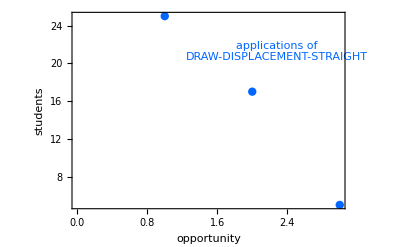

```mathematica
lc1=ListPlot[numberstudents[principle],Axes->False,Frame->True,BaseStyle->{FontSize->12},FrameLabel->{"opportunity","students"},PlotStyle->{Hue[0.6],PointSize[0.015]},RotateLabel->False,Epilog->{Hue[0.6],Text["applications of\n"<>principle,Scaled[{0.75,0.8}]]}]
```

```mathematica
Export["~/log/numberstudents.eps",lc1,"EPSTIFF",ImageSize->432]
```

~/log/numberstudents.eps

```mathematica
Export["~/log/numberstudents.tiff",lc1,ImageSize->432]
```

~/log/numberstudents.tiff

```mathematica
cutoff=3;
```

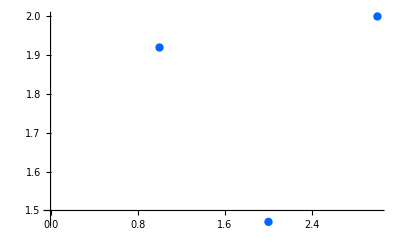

```mathematica
pavgerr=ListPlot[Take[avgerrors[principle],cutoff],DisplayFunction->Identity,PlotStyle->{Hue[0.6],PointSize[0.015]}]
```

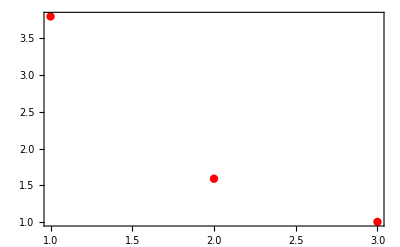

```mathematica
pavghint=ListPlot[Take[avghints[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0],PointSize[0.015]},DisplayFunction->Identity]
```

```mathematica
passist=Show[pavghint,pavgerr,Axes->False,Frame->True,BaseStyle->{FontSize->12},DisplayFunction->$DisplayFunction,RotateLabel->False,FrameLabel->{"opportunity","average\nnumber"},Epilog->{PointSize[0.015],{Text["before application of\n"<>principle,Scaled[{0.5,0.74}],{-1,1}]},{Hue[0],Point[Scaled[{0.48,0.88}]],Text["hints received",Scaled[{0.5,0.9}],{-1,1}]},{Hue[0.6],Point[Scaled[{0.48,0.8}]],Text["errors made",Scaled[{0.5,0.82}],{-1,1}]}}]
```

-Graphics-

```mathematica
Export["~/log/averageassistance.eps",passist,"EPSTIFF",ImageSize->432]
```

~/log/averageassistance.eps

```mathematica
Export["~/log/averageassistance.tiff",passist,ImageSize->432]
```

~/log/averageassistance.tiff

```mathematica
Column[Take[problemlist[principle],cutoff]]
```

{{elec3a,23},{elec6a,2}}
{{elec3a,2},{elec6a,15}}
{{elec6a,5}}

```mathematica
Column[Take[errornames[principle],cutoff]]
```

{{DEFAULT-WRONG-DIR,1},{DISTANCE-TRAVELLED-SHOULD-BE-DISPLACEMENT,28},{NON-EXISTENT-VARIABLE,2},{UNDEFINED-VARIABLES,1},{UNUSED-VARIABLES,5},{VECTOR-TIME,7},{VECTOR-WRONG-TIME-AND-DIRECTION,1},{VELOCITY-NOT-SPEED,3}}
{{DISTANCE-TRAVELLED-SHOULD-BE-DISPLACEMENT,2},{MISSING-NEGATION-ON-VECTOR-COMPONENT,1},{UNDEFINED-VARIABLES,4},{UNDIAGNOSED-EQN-ERROR,9},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,3},{VECTOR-TIME,3},{VELOCITY-SHOULD-BE-ZERO,1},{assoc-error-nil-show-hint,1},{assoc-error-t-show-hint,1}}
{{DEFAULT-WRONG-DIR,2},{USED-MAGNITUDE-INSTEAD-OF-COMPONENT,7},{VECTOR-TIME,1}}

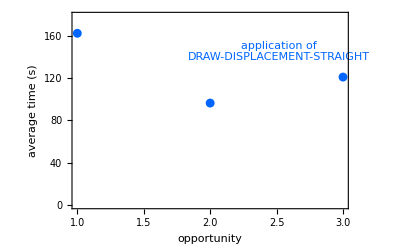

```mathematica
ptc=Block[{data=Take[avgtime[principle],cutoff]},ListPlot[data,PlotRange->{All,{0,1.1 Max[data]}},Frame->True,Axes->False,BaseStyle->{FontSize->12},FrameLabel->{"opportunity","average\ntime (s)"},PlotStyle->{Hue[0.6],PointSize[0.016]},RotateLabel->False,Epilog->{Hue[0.6],Text["application of\n"<>principle,Scaled[{0.75,0.8}]]}]]
```

```mathematica
Export["~/log/averagetime.eps",ptc,"EPSTIFF",ImageSize->432]
```

~/log/averagetime.eps

```mathematica
Export["~/log/averagetime.tiff",ptc,ImageSize->432]
```

~/log/averagetime.tiff

Fraction of students applying principle with no hints or errors

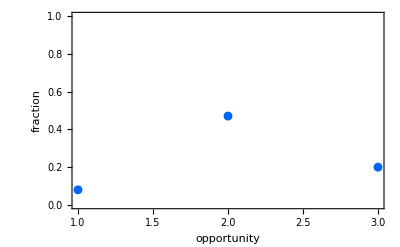

```mathematica
ListPlot[Take[noassistance[principle],cutoff],PlotRange->{All,{0,1}},Frame->True, FrameLabel->{"opportunity","fraction"},Axes->False,PlotStyle->{Hue[0.6],PointSize[0.016]}]
```

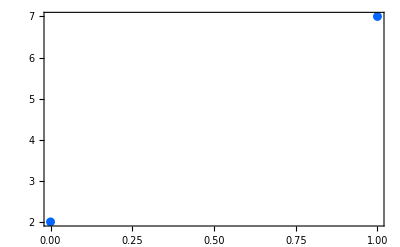

```mathematica
ListPlot[attemptsbeforeFNA[principle],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0.6],PointSize[0.016]}]
```

```mathematica
binthis[x_List,n_]:=Block[{min=Max[Max[x]/(2*(n+1/2)),Min[x]],width=(Max[x]-min)/n,h},Line[Join[{{min-width/2,0}},Flatten[Table[h=Length[Select[x,(cent-width/2<#≤cent+width/2)&]];{{cent-width/2,h},{cent+width/2,h}},{cent,min,Max[x],width}],1],{{Max[x]+width/2,0}}]]]
```

```mathematica
timebeforeFNA[principle]
```

{631,56,391,168,190,15,229,304,88}

```mathematica
binthis[timebeforeFNA[principle],3]
```

Line[{{0,0},{0,4},{1262/7,4},{1262/7,3},{2524/7,3},{2524/7,1},{3786/7,1},{3786/7,1},{5048/7,1},{5048/7,0}}]

```mathematica
5048./7
```

721.143

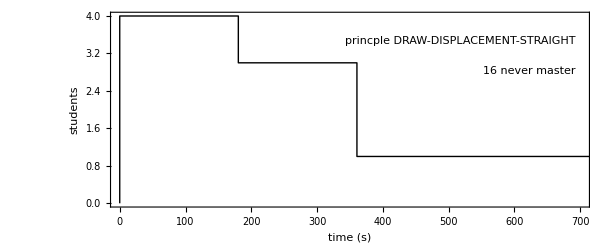

```mathematica
ptmaster=Show[Graphics[{binthis[timebeforeFNA[principle],3],Text[Row[{neverFNA[principle]," never master"}],Scaled[{0.97,0.7}],{1,0}],Text["princple "<>principle,Scaled[{0.97,0.85}],{1,0}]}],PlotRange->{{0,700},{0,4}},RotateLabel->False,Frame->True,BaseStyle->{FontSize->12},FrameLabel->{"time (s)","students"}]
```

```mathematica
Export["~/log/masterytime.eps",ptmaster,"EPSTIFF",ImageSize->432]
```

~/log/masterytime.eps

```mathematica
Export["~/log/masterytime.tiff",ptmaster,ImageSize->432]
```

~/log/masterytime.tiff

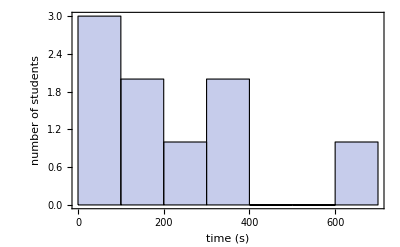

```mathematica
Histogram[timebeforeFNA[principle],(*PlotLabel->principle,*)HistogramCategories->6,FrameLabel->{"time (s)","number of students"},Frame->True]
```

```mathematica
Function[principle,Block[{cutoff=Length[Select[numberstudents[principle],#1>0&]],pavgerr,pavghint},If[Length[attemptsbeforeFNA[principle]]>1,pavgerr=ListPlot[Take[avgerrors[principle],cutoff],DisplayFunction->Identity,PlotStyle->{Hue[0.6],PointSize[0.015]}];pavghint=ListPlot[Take[avghints[principle],cutoff],PlotRange->All,Frame->True,Axes->False,PlotStyle->{Hue[0],PointSize[0.015]},DisplayFunction->Identity];Show[pavghint,pavgerr,Axes->False,Frame->True,BaseStyle->{FontSize->12},DisplayFunction->$DisplayFunction,RotateLabel->False,FrameLabel->{"opportunity","average\nnumber"},Epilog->{PointSize[0.015],{Text["before application of\n"<>principle,Scaled[{0.5,0.74}],{-1,1}]},{Hue[0],Point[Scaled[{0.48,0.88}]],Text["hints received",Scaled[{0.5,0.9}],{-1,1}]},{Hue[0.6],Point[Scaled[{0.48,0.8}]],Text["errors made",Scaled[{0.5,0.82}],{-1,1}]}}]]]]/@Take[(#1⟦2⟧&)/@Sort[({N[Mean[attemptsbeforeFNA[#1]]],#1}&)/@operators],-25]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Null,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Null,-Graphics-,Null,Null,Null,Null,Null}

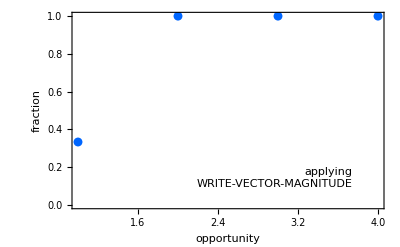
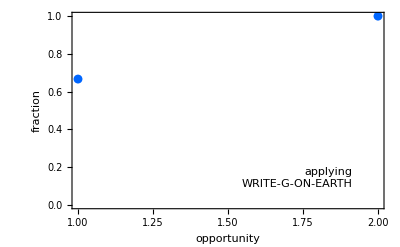
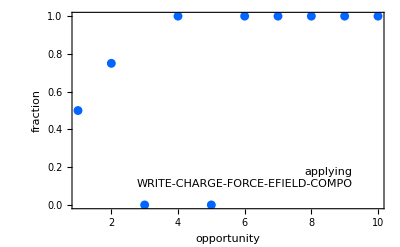
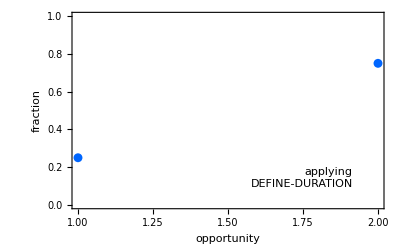
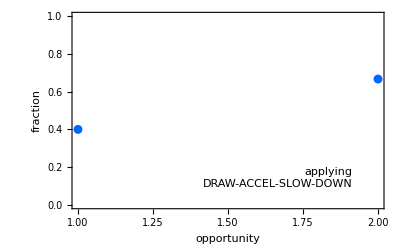
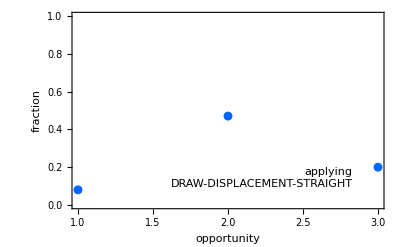
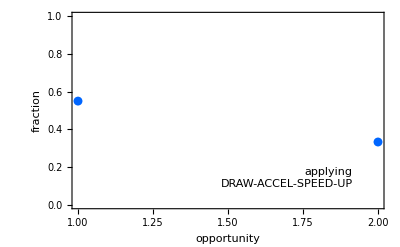
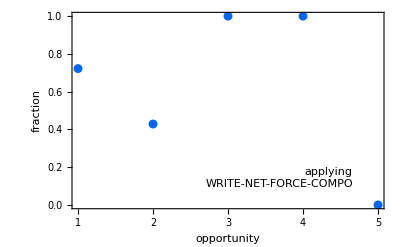
{Null,Null,Null,Null,Null,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Null,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Null,-Graphics-,Null,Null,Null,Null,Null}

```mathematica
Function[principle,Block[{cutoff=Length[numberstudents[principle]],pavgerr,pavghint},If[Length[attemptsbeforeFNA[principle]]>1,ListPlot[Take[noassistance[principle],cutoff],PlotRange->{All,{0,1}},Frame->True,BaseStyle->{FontSize->12},Axes->False,FrameLabel->{"opportunity","fraction"},PlotStyle->{Hue[0.6],PointSize[0.016]},Epilog->{PointSize[0.015],{Text["applying\n"<>principle,Scaled[{0.9,0.1}],{1,-1}]}}]]]]/@(#1⟦2⟧&)/@Sort[({N[Mean[attemptsbeforeFNA[#1]]],#1}&)/@operators]
```

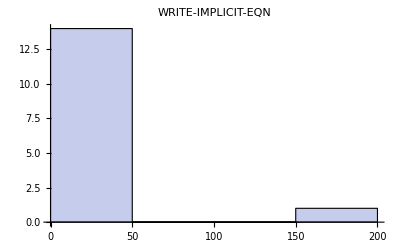
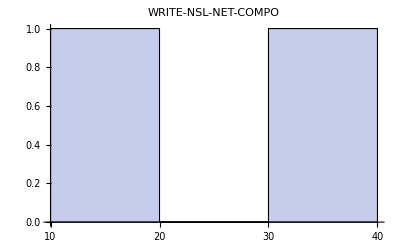
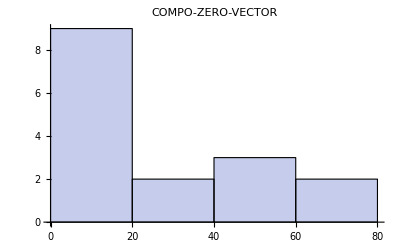
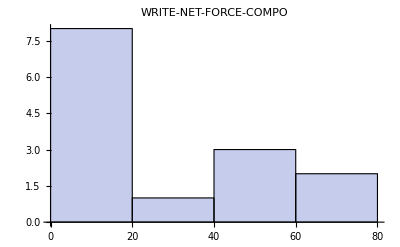
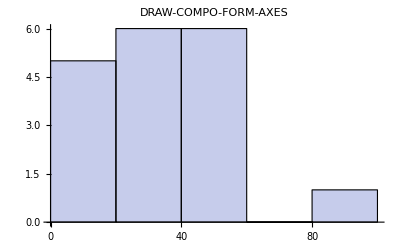
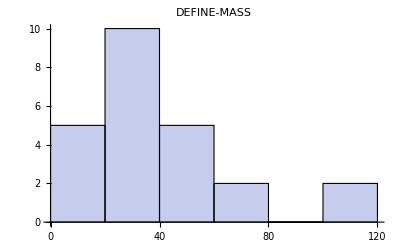
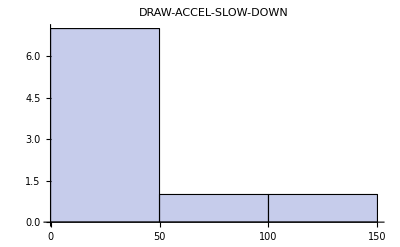
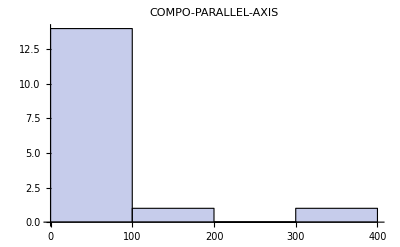

```mathematica
Map[If[Length[timebeforeFNA[#[[2]]]]>1,Histogram[timebeforeFNA[#[[2]]],PlotLabel->#[[2]]],{}]&,Sort[Map[{N[Mean[timebeforeFNA[#]]],#}&,operators]]]
```

### Fall linear model

```mathematica
<<"LinearRegression`"
```

```mathematica
<<"~/log/Fall2005-linear.out"
```

```mathematica
<<"~/log/junk.out"
```

```mathematica
mat=SparseArray[Map[(Take[#,2]->#[[-1]])&,Flatten[operatorinstances,1]],{Length[operatorinstances],Length[operators]}];tmat=Transpose[mat];
```

```mathematica
{Length[operators],MatrixRank[mat]}
```

{244,237}

```mathematica
Map[(#≥0)&,Map[t,operators]]
```

{t[ACCEL-AT-REST]≥0,t[ACCEL-CONSTANT-SPEED]≥0,t[APPLY-NET-WORK]≥0,t[AREA-OF-CIRCLE]≥0,t[AVG-ACCEL-UNKNOWN]≥0,t[BERNOULLI]≥0,t[CIRCUMFERENCE-OF-CIRCLE-R]≥0,t[COMPO-GENERAL-CASE]≥0,t[COMPO-GENERAL-CASE-UNKNOWN]≥0,t[COMPO-PARALLEL-AXIS]≥0,t[COMPO-PERPENDICULAR]≥0,t[COMPO-Z-AXIS]≥0,t[COMPO-ZERO-VECTOR]≥0,t[CONTINUITY]≥0,t[DEFINE-AMPLITUDE]≥0,t[DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION]≥0,t[DEFINE-AMPLITUDE-MAX-SPEED]≥0,t[DEFINE-ANGLE-BETWEEN-KNOWN]≥0,t[DEFINE-ANGULAR-FREQUENCY]≥0,t[DEFINE-AREA]≥0,t[DEFINE-AREA-AT]≥0,t[DEFINE-CHANGING-MASS]≥0,t[DEFINE-CHANGING-MOMENT-OF-INERTIA]≥0,t[DEFINE-CIRCUMFERENCE-OF-CIRCLE]≥0,t[DEFINE-COEF-FRICTION]≥0,t[DEFINE-COMPRESSION]≥0,t[DEFINE-DB-INTENSITY]≥0,t[DEFINE-DISTANCE]≥0,t[DEFINE-DURATION]≥0,t[DEFINE-FREQUENCY]≥0,t[DEFINE-GRAV-ENERGY]≥0,t[DEFINE-HEIGHT]≥0,t[DEFINE-INTENSITY]≥0,t[DEFINE-KINETIC-ENERGY]≥0,t[DEFINE-MASS]≥0,t[DEFINE-MASS-CHANGE-MAGNITUDE]≥0,t[DEFINE-MASS-DENSITY]≥0,t[DEFINE-MOMENT-OF-INERTIA]≥0,t[DEFINE-NET-DB-INTENSITY]≥0,t[DEFINE-NET-INTENSITY]≥0,t[DEFINE-NET-POWER-OUT]≥0,t[DEFINE-NET-POWER-VAR]≥0,t[DEFINE-NET-WORK]≥0,t[DEFINE-OBSERVED-FREQUENCY]≥0,t[DEFINE-PERIOD-VAR]≥0,t[DEFINE-POWER-VAR]≥0,t[DEFINE-PRESSURE]≥0,t[DEFINE-RADIUS-OF-CIRCLE]≥0,t[DEFINE-REVOLUTION-RADIUS]≥0,t[DEFINE-ROTATIONAL-ENERGY]≥0,t[DEFINE-SHAPE-LENGTH]≥0,t[DEFINE-SPEED]≥0,t[DEFINE-SPRING-CONSTANT]≥0,t[DEFINE-SPRING-ENERGY]≥0,t[DEFINE-STRING-TENSION]≥0,t[DEFINE-TOTAL-ENERGY]≥0,t[DEFINE-VOLUME]≥0,t[DEFINE-WAVE-SPEED]≥0,t[DEFINE-WAVELENGTH]≥0,t[DEFINE-WAVENUMBER]≥0,t[DEFINE-WIDTH]≥0,t[DEFINE-WNC]≥0,t[DEFINE-WORK]≥0,t[DRAW-ACCEL-CURVED-UNKNOWN]≥0,t[DRAW-ACCEL-FREE-FALL]≥0,t[DRAW-ACCEL-GIVEN-DIR]≥0,t[DRAW-ACCEL-UNKNOWN-NET-FORCE]≥0,t[DRAW-ACCELERATING]≥0,t[DRAW-ANG-ACCEL-UNKNOWN-DIR]≥0,t[DRAW-ANG-ACCELERATING]≥0,t[DRAW-ANG-DECELERATING]≥0,t[DRAW-ANG-DISPLACEMENT-ROTATING]≥0,t[DRAW-ANG-MOMENTUM-ROTATING]≥0,t[DRAW-ANG-VELOCITY-AT-REST]≥0,t[DRAW-ANG-VELOCITY-ROTATING]≥0,t[DRAW-APPLIED-FORCE]≥0,t[DRAW-AVG-VEL-FROM-DISPLACEMENT]≥0,t[DRAW-AVG-VEL-UNKNOWN]≥0,t[DRAW-BODY]≥0,t[DRAW-BUOYANT-FORCE]≥0,t[DRAW-CENTRIPETAL-ACCELERATION]≥0,t[DRAW-COMPO-FORM-AXES]≥0,t[DRAW-DECELERATING]≥0,t[DRAW-DISPLACEMENT-GIVEN-DIR]≥0,t[DRAW-DISPLACEMENT-PROJECTILE]≥0,t[DRAW-DISPLACEMENT-STRAIGHT]≥0,t[DRAW-DISPLACEMENT-UNKNOWN]≥0,t[DRAW-DISPLACEMENT-ZERO]≥0,t[DRAW-DRAG]≥0,t[DRAW-ENERGY-AXES]≥0,t[DRAW-FORCE-COMPOUND]≥0,t[DRAW-GRAV-FORCE]≥0,t[DRAW-IMPULSE-GIVEN-DIR]≥0,t[DRAW-IMPULSE-GIVEN-FORCE]≥0,t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR]≥0,t[DRAW-KINETIC-FRICTION]≥0,t[DRAW-MOMENTUM-AT-REST]≥0,t[DRAW-MOMENTUM-STRAIGHT]≥0,t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN]≥0,t[DRAW-NET-FORCE-FROM-ACCEL]≥0,t[DRAW-NET-TORQUE-FROM-ANG-ACCEL]≥0,t[DRAW-NET-TORQUE-NON-ROTATING]≥0,t[DRAW-NET-TORQUE-UNKNOWN-DIR]≥0,t[DRAW-NORMAL]≥0,t[DRAW-OPPOSITE-RELATIVE-POSITION]≥0,t[DRAW-PRESSURE]≥0,t[DRAW-REACTION-FORCE]≥0,t[DRAW-REL-VEL-VECTOR-UNKNOWN]≥0,t[DRAW-RELATIVE-POSITION]≥0,t[DRAW-RELATIVE-POSITION-UNKNOWN]≥0,t[DRAW-RELATIVE-VEL-GIVEN-DIR]≥0,t[DRAW-ROTATE-AXES]≥0,t[DRAW-SOUGHT-VECTOR-UNKNOWN]≥0,t[DRAW-SPRING-FORCE]≥0,t[DRAW-STATIC-FRICTION]≥0,t[DRAW-TENSION]≥0,t[DRAW-THRUST-FORCE]≥0,t[DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL]≥0,t[DRAW-TORQUE]≥0,t[DRAW-UNROTATED-AXES]≥0,t[DRAW-UNROTATED-AXES-FOR-ZCOMPS]≥0,t[DRAW-VECTOR-GIVEN-COMPOS]≥0,t[DRAW-VELOCITY-AT-REST]≥0,t[DRAW-VELOCITY-CURVED]≥0,t[DRAW-VELOCITY-CURVED-UNKNOWN]≥0,t[DRAW-VELOCITY-MOMENTARILY-AT-REST]≥0,t[DRAW-VELOCITY-STRAIGHT]≥0,t[DRAW-VELOCITY-STRAIGHT-UNKNOWN]≥0,t[DRAW-WEIGHT]≥0,t[DRAW-WEIGHT-AT-CM]≥0,t[DRAW-ZERO-RELATIVE-POSITION]≥0,t[DRAW-ZERO-RELATIVE-VEL]≥0,t[FREQUENCY-OF-WAVE]≥0,t[GIVEN-FRACTION]≥0,t[KINETIC-FRICTION-LAW]≥0,t[MAKE-DOPPLER-FREQUENCY]≥0,t[MASS-PER-LENGTH]≥0,t[MASS-PER-LENGTH-EQUATION]≥0,t[MAX-TRANSVERSE-ABS-ACCELERATION-WAVE]≥0,t[MAX-TRANSVERSE-SPEED-WAVE]≥0,t[NTL]≥0,t[OPPOSITE-RELATIVE-POSITION]≥0,t[PENDULUM-OSCILLATION]≥0,t[PERIOD-OF-WAVE]≥0,t[PRESSURE-AT-OPEN-TO-ATMOSPHERE]≥0,t[PRESSURE-FORCE]≥0,t[PRESSURE-HEIGHT-FLUID]≥0,t[SDD-CONSTVEL-COMPO]≥0,t[SELECT-MC-ANSWER]≥0,t[SPEED-EQUALS-WAVE-SPEED]≥0,t[SPRING-LAW-COMPRESSION]≥0,t[SPRING-MASS-OSCILLATION]≥0,t[STATIC-FRICTION-LAW]≥0,t[USE-CONST-VX]≥0,t[WAVE-SPEED-STRING]≥0,t[WAVENUMBER-LAMBDA-WAVE]≥0,t[WRITE-ANG-MOMENTUM]≥0,t[WRITE-ANG-SDD]≥0,t[WRITE-ARCHIMEDES]≥0,t[WRITE-AVG-ACCEL-COMPO]≥0,t[WRITE-AVG-VEL-COMPO]≥0,t[WRITE-BEAT-FREQUENCY]≥0,t[WRITE-CENTER-OF-MASS-COMPO]≥0,t[WRITE-CENTRIPETAL-ACCEL]≥0,t[WRITE-CHANGE-ME-TOP]≥0,t[WRITE-CONNECTED-ACCELS]≥0,t[WRITE-CONNECTED-VELOCITIES]≥0,t[WRITE-CONS-ANGMOM]≥0,t[WRITE-CONS-ANGMOM-JOIN]≥0,t[WRITE-CONS-KE-ELASTIC]≥0,t[WRITE-CONS-LINMOM-COMPO]≥0,t[WRITE-CONS-LINMOM-COMPO-JOIN]≥0,t[WRITE-CONS-LINMOM-COMPO-SPLIT]≥0,t[WRITE-DENSITY]≥0,t[WRITE-DISPLACEMENT-DISTANCE]≥0,t[WRITE-ENERGY-CONS]≥0,t[WRITE-EQUALITY]≥0,t[WRITE-FORCE-COMPOUND]≥0,t[WRITE-FREE-FALL-ACCEL]≥0,t[WRITE-G-ON-EARTH]≥0,t[WRITE-GRAV-ENERGY]≥0,t[WRITE-HARMONIC-OF]≥0,t[WRITE-HEIGHT-DY-COMPO]≥0,t[WRITE-I-COMPOUND]≥0,t[WRITE-I-HOOP-CM]≥0,t[WRITE-I-RECT-CM]≥0,t[WRITE-I-ROD-CM]≥0,t[WRITE-I-ROD-END]≥0,t[WRITE-IMPLICIT-EQN]≥0,t[WRITE-IMPULSE-COMPO]≥0,t[WRITE-IMPULSE-MOMENTUM-COMPO]≥0,t[WRITE-INST-POWER]≥0,t[WRITE-INTENSITY-TO-DECIBELS]≥0,t[WRITE-INTENSITY-TO-POWER]≥0,t[WRITE-KINETIC-ENERGY]≥0,t[WRITE-KNOWN-VALUE-EQN]≥0,t[WRITE-LINEAR-VEL]≥0,t[WRITE-LK-NO-S-COMPO]≥0,t[WRITE-LK-NO-T-COMPO]≥0,t[WRITE-LK-NO-VF-COMPO]≥0,t[WRITE-MAG-TORQUE]≥0,t[WRITE-MASS-COMPOUND]≥0,t[WRITE-MOMENTUM-COMPO]≥0,t[WRITE-NET-INTENSITY]≥0,t[WRITE-NET-POWER]≥0,t[WRITE-NET-TORQUE]≥0,t[WRITE-NFL-COMPO]≥0,t[WRITE-NL-ROTATION]≥0,t[WRITE-NSL-COMPO]≥0,t[WRITE-NSL-NET-COMPO]≥0,t[WRITE-NTL-VECTOR]≥0,t[WRITE-NULL-SPRING-ENERGY]≥0,t[WRITE-PERIOD-CIRCULAR]≥0,t[WRITE-POWER]≥0,t[WRITE-PYTH-THM]≥0,t[WRITE-RELATIVE-VEL-COMPO]≥0,t[WRITE-RK-NO-S]≥0,t[WRITE-RK-NO-T]≥0,t[WRITE-RK-NO-VF]≥0,t[WRITE-ROLLING-VEL]≥0,t[WRITE-ROTATIONAL-ENERGY]≥0,t[WRITE-SDD]≥0,t[WRITE-SPEED-OF-WAVE]≥0,t[WRITE-SPRING-ENERGY]≥0,t[WRITE-SUM-DISP-COMPO]≥0,t[WRITE-SUM-DISTANCES]≥0,t[WRITE-SUM-TIMES]≥0,t[WRITE-TENSIONS-EQUAL]≥0,t[WRITE-THRUST-FORCE]≥0,t[WRITE-THRUST-FORCE-COMPO]≥0,t[WRITE-TIMELESS-BEAT-FREQUENCY]≥0,t[WRITE-TORQUE-ZC]≥0,t[WRITE-TOTAL-ENERGY-TOP]≥0,t[WRITE-UG]≥0,t[WRITE-UG-CIRCULAR]≥0,t[WRITE-VALUE-OF-ATMOSPHERE]≥0,t[WRITE-VOLUME-COMPOUND]≥0,t[WRITE-WAVE-SPEED-LIGHT]≥0,t[WRITE-WNC]≥0,t[WRITE-WORK]≥0,t[WRITE-WORK-DELTA-KE]≥0,t[WRITE-ZERO-WORK]≥0,t[WT-LAW]≥0,t[WT-LAW-CM]≥0}

```mathematica
Block[{tt=Map[t,operators],expr,expr2},
NMinimize[{expr=mat.tt-N[eachtime];expr2=expr.expr,Map[(#≥0)&,tt]},tt,StepMonitor:>Print[expr2]]]
```

5.88537×10^9

5.82113×10^9

5.82113×10^9

5.82113×10^9

«28 more identical outputs»

$Aborted

```mathematica
Length[mat]-9295
```

244

```mathematica
NullSpace[mat].operators
```

{-DEFINE-ROTATIONAL-ENERGY-2 WRITE-I-ROD-END-2 WRITE-ROLLING-VEL+2 WRITE-ROTATIONAL-ENERGY,-DEFINE-NET-INTENSITY+WRITE-NET-INTENSITY,-DEFINE-WIDTH+WRITE-I-RECT-CM,-3 DRAW-AVG-VEL-UNKNOWN+WRITE-DISPLACEMENT-DISTANCE,-DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION+MAX-TRANSVERSE-ABS-ACCELERATION-WAVE,-DEFINE-WIDTH+DRAW-ANG-ACCEL-UNKNOWN-DIR,-CIRCUMFERENCE-OF-CIRCLE-R+DEFINE-CIRCUMFERENCE-OF-CIRCLE}

```mathematica
Regress[Transpose[Append[tmat,eachtime]],Map[t,operators],Map[t,operators],IncludeConstant->False,RegressionReport->{ParameterTable,RSquared,EstimatedVariance}]
```

DesignedRegress::rank: Warning: the rank of the design matrix is 237, less than full rank 244. Only 237 of the 244 basis functions "are" needed to provide this fit. Try using a different model or greater precision.

DesignedRegress::rsqr: Warning: the RSquared and AdjustedRSquared diagnostics are redefined when there is no constant term in the model.

{ParameterTable→ | Estimate | SE | TStat | PValue
t[ACCEL-AT-REST] | 80.967 | 25.3104 | 3.19896 | 0.00138386
t[ACCEL-CONSTANT-SPEED] | -67.8813 | 55.5911 | -1.22108 | 0.222086
t[APPLY-NET-WORK] | -4.07949 | 78.2359 | -0.0521434 | 0.958416
t[AREA-OF-CIRCLE] | 177.765 | 116.289 | 1.52865 | 0.126386
t[AVG-ACCEL-UNKNOWN] | 328.529 | 424.562 | 0.773808 | 0.439064
t[BERNOULLI] | -107.203 | 98.3689 | -1.08981 | 0.275826
t[CIRCUMFERENCE-OF-CIRCLE-R] | 228.276 | 167.322 | 1.36429 | 0.17251
t[COMPO-GENERAL-CASE] | 69.2123 | 7.94541 | 8.71098 | 0.
t[COMPO-GENERAL-CASE-UNKNOWN] | 37.0979 | 22.1728 | 1.67313 | 0.0943358
t[COMPO-PARALLEL-AXIS] | 30.3785 | 5.6898 | 5.33911 | 9.56094×10^-8
t[COMPO-PERPENDICULAR] | 92.4076 | 13.0503 | 7.08088 | 1.53655×10^-12
t[COMPO-Z-AXIS] | 34.851 | 19.0518 | 1.82928 | 0.0673899
t[COMPO-ZERO-VECTOR] | 18.5544 | 29.5114 | 0.628719 | 0.529548
t[CONTINUITY] | -204.751 | 256.667 | -0.79773 | 0.425047
t[DEFINE-AMPLITUDE] | 128.878 | 93.7455 | 1.37477 | 0.169237
t[DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[DEFINE-AMPLITUDE-MAX-SPEED] | -392.881 | 527.634 | -0.744608 | 0.456528
t[DEFINE-ANGLE-BETWEEN-KNOWN] | 103.567 | 19.7253 | 5.25048 | 1.55054×10^-7
t[DEFINE-ANGULAR-FREQUENCY] | 114.018 | 100.421 | 1.1354 | 0.256238
t[DEFINE-AREA] | -122.432 | 129.508 | -0.945362 | 0.344499
t[DEFINE-AREA-AT] | 123.76 | 130.837 | 0.945911 | 0.344219
t[DEFINE-CHANGING-MASS] | -4.66224 | 81.9807 | -0.05687 | 0.95465
t[DEFINE-CHANGING-MOMENT-OF-INERTIA] | 70.2317 | 64.6606 | 1.08616 | 0.277437
t[DEFINE-CIRCUMFERENCE-OF-CIRCLE] | 228.276 | 167.322 | 1.36429 | 0.17251
t[DEFINE-COEF-FRICTION] | -54.7711 | 257.4 | -0.212785 | 0.831499
t[DEFINE-COMPRESSION] | 151.524 | 68.7349 | 2.20447 | 0.0275154
t[DEFINE-DB-INTENSITY] | 40.9846 | 301.723 | 0.135835 | 0.891954
t[DEFINE-DISTANCE] | 189.492 | 60.3756 | 3.13856 | 0.00170313
t[DEFINE-DURATION] | 57.235 | 29.3567 | 1.94964 | 0.0512489
t[DEFINE-FREQUENCY] | 55.4145 | 23.6089 | 2.34719 | 0.0189366
t[DEFINE-GRAV-ENERGY] | -74.1932 | 52.3352 | -1.41765 | 0.156326
t[DEFINE-HEIGHT] | 54.2195 | 27.3709 | 1.98092 | 0.0476301
t[DEFINE-INTENSITY] | -27.0683 | 318.158 | -0.085078 | 0.932201
t[DEFINE-KINETIC-ENERGY] | 104.202 | 34.9183 | 2.98416 | 0.00285094
t[DEFINE-MASS] | -16.1648 | 16.7006 | -0.967918 | 0.33311
t[DEFINE-MASS-CHANGE-MAGNITUDE] | 45.791 | 133.766 | 0.342321 | 0.732117
t[DEFINE-MASS-DENSITY] | 88.664 | 67.0231 | 1.32289 | 0.185905
t[DEFINE-MOMENT-OF-INERTIA] | 46.9011 | 68.0459 | 0.689258 | 0.490678
t[DEFINE-NET-DB-INTENSITY] | 441.763 | 454.65 | 0.971657 | 0.331247
t[DEFINE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[DEFINE-NET-POWER-OUT] | 235.957 | 117.7 | 2.00473 | 0.0450207
t[DEFINE-NET-POWER-VAR] | 222.028 | 215.685 | 1.02941 | 0.303315
t[DEFINE-NET-WORK] | 152.34 | 61.7607 | 2.46662 | 0.0136576
t[DEFINE-OBSERVED-FREQUENCY] | 123.8 | 50.7794 | 2.43799 | 0.0147877
t[DEFINE-PERIOD-VAR] | 118.314 | 62.5803 | 1.89059 | 0.0587095
t[DEFINE-POWER-VAR] | 189.127 | 88.7836 | 2.1302 | 0.0331813
t[DEFINE-PRESSURE] | -11.0693 | 49.7567 | -0.222469 | 0.823953
t[DEFINE-RADIUS-OF-CIRCLE] | 55.2396 | 92.8854 | 0.594707 | 0.552054
t[DEFINE-REVOLUTION-RADIUS] | 120.222 | 80.5745 | 1.49207 | 0.135716
t[DEFINE-ROTATIONAL-ENERGY] | 781.191 | 207.52 | 3.76441 | 0.00016797
t[DEFINE-SHAPE-LENGTH] | 117.062 | 60.8239 | 1.92461 | 0.0543092
t[DEFINE-SPEED] | 140.042 | 56.422 | 2.48205 | 0.0130805
t[DEFINE-SPRING-CONSTANT] | 40.1465 | 88.5878 | 0.453183 | 0.650427
t[DEFINE-SPRING-ENERGY] | -43.8644 | 71.0073 | -0.617744 | 0.536759
t[DEFINE-STRING-TENSION] | 97.9443 | 90.7998 | 1.07868 | 0.280756
t[DEFINE-TOTAL-ENERGY] | 6.94647 | 45.1786 | 0.153756 | 0.877806
t[DEFINE-VOLUME] | 9.92488 | 79.1301 | 0.125425 | 0.90019
t[DEFINE-WAVE-SPEED] | 55.387 | 43.4297 | 1.27533 | 0.202225
t[DEFINE-WAVELENGTH] | 79.6269 | 39.0117 | 2.0411 | 0.0412688
t[DEFINE-WAVENUMBER] | 70.7439 | 121.209 | 0.583653 | 0.559468
t[DEFINE-WIDTH] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DEFINE-WNC] | 278.881 | 64.8924 | 4.29759 | 0.0000174421
t[DEFINE-WORK] | 96.4006 | 36.819 | 2.61823 | 0.00885318
t[DRAW-ACCEL-CURVED-UNKNOWN] | 31.295 | 82.5537 | 0.379087 | 0.704632
t[DRAW-ACCEL-FREE-FALL] | 257.718 | 70.6201 | 3.64936 | 0.00026434
t[DRAW-ACCEL-GIVEN-DIR] | -61.8253 | 22.3079 | -2.77145 | 0.00559174
t[DRAW-ACCEL-UNKNOWN-NET-FORCE] | 148.71 | 75.2507 | 1.97619 | 0.0481628
t[DRAW-ACCELERATING] | 154.382 | 25.7168 | 6.00316 | 2.00756×10^-9
t[DRAW-ANG-ACCEL-UNKNOWN-DIR] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DRAW-ANG-ACCELERATING] | -58.7854 | 86.1863 | -0.682074 | 0.495209
t[DRAW-ANG-DECELERATING] | -39.3732 | 92.3575 | -0.426313 | 0.66989
t[DRAW-ANG-DISPLACEMENT-ROTATING] | 116.223 | 78.1264 | 1.48763 | 0.136883
t[DRAW-ANG-MOMENTUM-ROTATING] | 50.6111 | 58.4893 | 0.865306 | 0.386893
t[DRAW-ANG-VELOCITY-AT-REST] | 100.187 | 106.415 | 0.941478 | 0.346485
t[DRAW-ANG-VELOCITY-ROTATING] | 57.163 | 40.9226 | 1.39686 | 0.16249
t[DRAW-APPLIED-FORCE] | -45.0335 | 13.8226 | -3.25797 | 0.00112616
t[DRAW-AVG-VEL-FROM-DISPLACEMENT] | -166.314 | 192.527 | -0.863848 | 0.387694
t[DRAW-AVG-VEL-UNKNOWN] | 325.928 | 232.493 | 1.40188 | 0.160983
t[DRAW-BODY] | 31.1038 | 14.5077 | 2.14396 | 0.0320621
t[DRAW-BUOYANT-FORCE] | 28.9033 | 78.27 | 0.369277 | 0.71193
t[DRAW-CENTRIPETAL-ACCELERATION] | 76.4552 | 149.863 | 0.510166 | 0.609947
t[DRAW-COMPO-FORM-AXES] | 179.076 | 28.7187 | 6.23551 | 4.69917×10^-10
t[DRAW-DECELERATING] | 175.55 | 53.2887 | 3.29433 | 0.000990274
t[DRAW-DISPLACEMENT-GIVEN-DIR] | -42.0221 | 15.7591 | -2.66653 | 0.00767723
t[DRAW-DISPLACEMENT-PROJECTILE] | 202.068 | 51.7773 | 3.90265 | 0.0000958185
t[DRAW-DISPLACEMENT-STRAIGHT] | 344.54 | 36.141 | 9.53322 | 0.
t[DRAW-DISPLACEMENT-UNKNOWN] | 334.665 | 95.7785 | 3.49415 | 0.000477782
t[DRAW-DISPLACEMENT-ZERO] | 348.907 | 423.27 | 0.824312 | 0.409784
t[DRAW-DRAG] | -96.7798 | 55.713 | -1.73711 | 0.0824003
t[DRAW-ENERGY-AXES] | -118.13 | 48.7279 | -2.42428 | 0.0153578
t[DRAW-FORCE-COMPOUND] | 174.372 | 80.1326 | 2.17604 | 0.0295774
t[DRAW-GRAV-FORCE] | 297.31 | 101.715 | 2.92297 | 0.0034755
t[DRAW-IMPULSE-GIVEN-DIR] | 513.41 | 129.231 | 3.97283 | 0.000071561
t[DRAW-IMPULSE-GIVEN-FORCE] | 57.8593 | 128.187 | 0.451368 | 0.651735
t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR] | 78.4329 | 160.953 | 0.487304 | 0.626054
t[DRAW-KINETIC-FRICTION] | -34.5082 | 52.6009 | -0.656039 | 0.511815
t[DRAW-MOMENTUM-AT-REST] | -3.65401 | 59.9671 | -0.0609336 | 0.951413
t[DRAW-MOMENTUM-STRAIGHT] | -23.113 | 24.9523 | -0.92629 | 0.354319
t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN] | 540.225 | 101.117 | 5.34259 | 9.37932×10^-8
t[DRAW-NET-FORCE-FROM-ACCEL] | -49.9904 | 95.2467 | -0.524852 | 0.599699
t[DRAW-NET-TORQUE-FROM-ANG-ACCEL] | 47.9927 | 114.392 | 0.419548 | 0.674826
t[DRAW-NET-TORQUE-NON-ROTATING] | -142.135 | 90.7058 | -1.56699 | 0.117152
t[DRAW-NET-TORQUE-UNKNOWN-DIR] | -91.259 | 98.3451 | -0.927946 | 0.353459
t[DRAW-NORMAL] | 98.5385 | 20.0736 | 4.90885 | 9.3171×10^-7
t[DRAW-OPPOSITE-RELATIVE-POSITION] | -314.146 | 310.526 | -1.01166 | 0.311729
t[DRAW-PRESSURE] | 229.818 | 62.3684 | 3.68485 | 0.000230135
t[DRAW-REACTION-FORCE] | 286.424 | 45.1449 | 6.34454 | 2.33497×10^-10
t[DRAW-REL-VEL-VECTOR-UNKNOWN] | 450.924 | 111.463 | 4.0455 | 0.0000526341
t[DRAW-RELATIVE-POSITION] | 141.617 | 30.0631 | 4.71066 | 2.50499×10^-6
t[DRAW-RELATIVE-POSITION-UNKNOWN] | 167.587 | 83.3717 | 2.01012 | 0.0444472
t[DRAW-RELATIVE-VEL-GIVEN-DIR] | 12.954 | 31.3787 | 0.412827 | 0.679743
t[DRAW-ROTATE-AXES] | 154.768 | 22.2603 | 6.95265 | 3.82649×10^-12
t[DRAW-SOUGHT-VECTOR-UNKNOWN] | 289.944 | 98.1955 | 2.95272 | 0.00315771
t[DRAW-SPRING-FORCE] | -28.9917 | 52.6714 | -0.550426 | 0.58204
t[DRAW-STATIC-FRICTION] | 121.693 | 32.6053 | 3.7323 | 0.000190873
t[DRAW-TENSION] | -1.04188 | 14.6314 | -0.0712083 | 0.943233
t[DRAW-THRUST-FORCE] | 23.6358 | 79.8037 | 0.296174 | 0.767104
t[DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL] | -92.586 | 102.852 | -0.900189 | 0.368043
t[DRAW-TORQUE] | 113.253 | 51.4969 | 2.19921 | 0.0278872
t[DRAW-UNROTATED-AXES] | 3.34173 | 38.2198 | 0.0874345 | 0.930328
t[DRAW-UNROTATED-AXES-FOR-ZCOMPS] | 22.9658 | 63.0891 | 0.364022 | 0.71585
t[DRAW-VECTOR-GIVEN-COMPOS] | 114.142 | 46.829 | 2.43743 | 0.0148107
t[DRAW-VELOCITY-AT-REST] | -17.1141 | 42.2468 | -0.405098 | 0.685415
t[DRAW-VELOCITY-CURVED] | 1.00682 | 28.442 | 0.0353991 | 0.971762
t[DRAW-VELOCITY-CURVED-UNKNOWN] | 171.793 | 53.5434 | 3.20847 | 0.00133895
t[DRAW-VELOCITY-MOMENTARILY-AT-REST] | 64.617 | 28.0073 | 2.30715 | 0.0210684
t[DRAW-VELOCITY-STRAIGHT] | 54.5852 | 15.9453 | 3.42328 | 0.000621369
t[DRAW-VELOCITY-STRAIGHT-UNKNOWN] | -176.867 | 80.1487 | -2.20673 | 0.0273572
t[DRAW-WEIGHT] | -54.9103 | 24.4593 | -2.24496 | 0.0247939
t[DRAW-WEIGHT-AT-CM] | 13.959 | 262.833 | 0.05311 | 0.957645
t[DRAW-ZERO-RELATIVE-POSITION] | 99.7001 | 101.476 | 0.982497 | 0.325881
t[DRAW-ZERO-RELATIVE-VEL] | 17.2664 | 35.3219 | 0.48883 | 0.624974
t[FREQUENCY-OF-WAVE] | 87.1353 | 102.659 | 0.848786 | 0.396022
t[GIVEN-FRACTION] | -67.378 | 55.6139 | -1.21153 | 0.225723
t[KINETIC-FRICTION-LAW] | 152.486 | 394.556 | 0.386475 | 0.699154
t[MAKE-DOPPLER-FREQUENCY] | 29.1796 | 55.9538 | 0.521493 | 0.602035
t[MASS-PER-LENGTH] | -279.465 | 158.671 | -1.76128 | 0.0782233
t[MASS-PER-LENGTH-EQUATION] | 60.2706 | 108.495 | 0.555516 | 0.578555
t[MAX-TRANSVERSE-ABS-ACCELERATION-WAVE] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[MAX-TRANSVERSE-SPEED-WAVE] | 219.984 | 301.487 | 0.729664 | 0.465614
t[NTL] | -183.209 | 113.421 | -1.6153 | 0.106279
t[OPPOSITE-RELATIVE-POSITION] | 135.237 | 149.783 | 0.902882 | 0.366612
t[PENDULUM-OSCILLATION] | -78.6796 | 89.8948 | -0.875241 | 0.381465
t[PERIOD-OF-WAVE] | -17.9274 | 56.4782 | -0.317421 | 0.750931
t[PRESSURE-AT-OPEN-TO-ATMOSPHERE] | 120.782 | 73.8191 | 1.63619 | 0.101834
t[PRESSURE-FORCE] | -165.81 | 69.827 | -2.37459 | 0.0175886
t[PRESSURE-HEIGHT-FLUID] | 125.971 | 112.027 | 1.12447 | 0.260843
t[SDD-CONSTVEL-COMPO] | 113.242 | 32.6259 | 3.47092 | 0.00052104
t[SELECT-MC-ANSWER] | 19.9777 | 5.98339 | 3.33886 | 0.000844552
t[SPEED-EQUALS-WAVE-SPEED] | -142.704 | 119.366 | -1.19551 | 0.231916
t[SPRING-LAW-COMPRESSION] | -60.1954 | 87.4575 | -0.688281 | 0.491293
t[SPRING-MASS-OSCILLATION] | 113.865 | 92.3935 | 1.23239 | 0.217835
t[STATIC-FRICTION-LAW] | -254.965 | 389.478 | -0.654634 | 0.512719
t[USE-CONST-VX] | -51.4276 | 80.9605 | -0.635219 | 0.525301
t[WAVE-SPEED-STRING] | 258.771 | 130.422 | 1.9841 | 0.0472735
t[WAVENUMBER-LAMBDA-WAVE] | 158.464 | 128.815 | 1.23017 | 0.218664
t[WRITE-ANG-MOMENTUM] | -0.954156 | 41.0137 | -0.0232643 | 0.98144
t[WRITE-ANG-SDD] | -20.3594 | 85.7647 | -0.237387 | 0.812362
t[WRITE-ARCHIMEDES] | 38.1219 | 91.0601 | 0.418646 | 0.675485
t[WRITE-AVG-ACCEL-COMPO] | -78.4195 | 29.6531 | -2.64456 | 0.00819342
t[WRITE-AVG-VEL-COMPO] | 99.0789 | 113.954 | 0.869468 | 0.384614
t[WRITE-BEAT-FREQUENCY] | -86.1302 | 137.112 | -0.628175 | 0.529905
t[WRITE-CENTER-OF-MASS-COMPO] | -254.721 | 94.2254 | -2.70331 | 0.00687769
t[WRITE-CENTRIPETAL-ACCEL] | 13.7309 | 145.037 | 0.0946717 | 0.924578
t[WRITE-CHANGE-ME-TOP] | 333.788 | 116.404 | 2.8675 | 0.00414663
t[WRITE-CONNECTED-ACCELS] | 221.366 | 146.502 | 1.51101 | 0.13082
t[WRITE-CONNECTED-VELOCITIES] | 65.6251 | 128.219 | 0.511822 | 0.608788
t[WRITE-CONS-ANGMOM] | -56.6764 | 124.027 | -0.456967 | 0.647706
t[WRITE-CONS-ANGMOM-JOIN] | -65.3542 | 130.893 | -0.499295 | 0.617583
t[WRITE-CONS-KE-ELASTIC] | 304.566 | 161.369 | 1.88739 | 0.0591389
t[WRITE-CONS-LINMOM-COMPO] | -93.608 | 61.2753 | -1.52766 | 0.126631
t[WRITE-CONS-LINMOM-COMPO-JOIN] | -267.578 | 110.74 | -2.41627 | 0.0156996
t[WRITE-CONS-LINMOM-COMPO-SPLIT] | -259.482 | 60.9167 | -4.25962 | 0.0000206788
t[WRITE-DENSITY] | -138.118 | 78.8337 | -1.75202 | 0.0798037
t[WRITE-DISPLACEMENT-DISTANCE] | 108.643 | 77.4977 | 1.40188 | 0.160983
t[WRITE-ENERGY-CONS] | 104.039 | 60.0589 | 1.73229 | 0.0832556
t[WRITE-EQUALITY] | 88.827 | 30.0219 | 2.95874 | 0.00309677
t[WRITE-FORCE-COMPOUND] | -153.919 | 77.0469 | -1.99773 | 0.0457755
t[WRITE-FREE-FALL-ACCEL] | -425.253 | 84.4599 | -5.03497 | 4.86904×10^-7
t[WRITE-G-ON-EARTH] | 13.2466 | 26.987 | 0.490851 | 0.623544
t[WRITE-GRAV-ENERGY] | 201.762 | 40.4384 | 4.98937 | 6.16728×10^-7
t[WRITE-HARMONIC-OF] | 17.0743 | 31.4916 | 0.542184 | 0.587704
t[WRITE-HEIGHT-DY-COMPO] | -312.416 | 64.5463 | -4.84018 | 1.31807×10^-6
t[WRITE-I-COMPOUND] | 61.4778 | 156.678 | 0.392384 | 0.694783
t[WRITE-I-HOOP-CM] | -21.843 | 120.26 | -0.181631 | 0.855876
t[WRITE-I-RECT-CM] | -188.169 | 148.369 | -1.26825 | 0.204741
t[WRITE-I-ROD-CM] | 48.08 | 102.067 | 0.471061 | 0.637608
t[WRITE-I-ROD-END] | -2154.69 | 625.819 | -3.443 | 0.000577834
t[WRITE-IMPLICIT-EQN] | 36.6267 | 9.2686 | 3.9517 | 0.0000781725
t[WRITE-IMPULSE-COMPO] | 247.881 | 156.857 | 1.58029 | 0.114074
t[WRITE-IMPULSE-MOMENTUM-COMPO] | -305.304 | 83.4567 | -3.65823 | 0.000255367
t[WRITE-INST-POWER] | 129.988 | 106.696 | 1.2183 | 0.223142
t[WRITE-INTENSITY-TO-DECIBELS] | -16.5042 | 78.7797 | -0.209498 | 0.834064
t[WRITE-INTENSITY-TO-POWER] | -89.7419 | 138.466 | -0.648115 | 0.516927
t[WRITE-KINETIC-ENERGY] | -99.563 | 31.929 | -3.11827 | 0.00182475
t[WRITE-KNOWN-VALUE-EQN] | 39.187 | 8.05835 | 4.8629 | 1.17574×10^-6
t[WRITE-LINEAR-VEL] | 67.145 | 76.4833 | 0.877903 | 0.380019
t[WRITE-LK-NO-S-COMPO] | 33.4984 | 35.5711 | 0.941732 | 0.346354
t[WRITE-LK-NO-T-COMPO] | 350.943 | 47.9222 | 7.32319 | 2.62235×10^-13
t[WRITE-LK-NO-VF-COMPO] | 95.0598 | 53.5847 | 1.77401 | 0.0760945
t[WRITE-MAG-TORQUE] | -28.1304 | 38.9178 | -0.722817 | 0.469811
t[WRITE-MASS-COMPOUND] | 245.531 | 59.0033 | 4.16131 | 0.0000319282
t[WRITE-MOMENTUM-COMPO] | 93.4338 | 20.9439 | 4.46114 | 8.24838×10^-6
t[WRITE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[WRITE-NET-POWER] | -295.645 | 228.668 | -1.2929 | 0.196078
t[WRITE-NET-TORQUE] | 73.5505 | 95.4385 | 0.770659 | 0.440929
t[WRITE-NFL-COMPO] | 38.428 | 15.2433 | 2.52097 | 0.0117198
t[WRITE-NL-ROTATION] | -55.4693 | 135.707 | -0.408744 | 0.682737
t[WRITE-NSL-COMPO] | -93.6298 | 22.6954 | -4.1255 | 0.0000373153
t[WRITE-NSL-NET-COMPO] | 101.962 | 110.935 | 0.919119 | 0.358057
t[WRITE-NTL-VECTOR] | 169.542 | 85.4327 | 1.98451 | 0.0472288
t[WRITE-NULL-SPRING-ENERGY] | 228.357 | 65.8268 | 3.46906 | 0.000524643
t[WRITE-PERIOD-CIRCULAR] | 140.314 | 105.439 | 1.33076 | 0.183301
t[WRITE-POWER] | -38.8913 | 101.811 | -0.381997 | 0.702472
t[WRITE-PYTH-THM] | -157.875 | 112.202 | -1.40707 | 0.15944
t[WRITE-RELATIVE-VEL-COMPO] | -23.6467 | 52.2913 | -0.452211 | 0.651127
t[WRITE-RK-NO-S] | 10.359 | 80.311 | 0.128986 | 0.897372
t[WRITE-RK-NO-T] | -17.0348 | 122.345 | -0.139235 | 0.889267
t[WRITE-RK-NO-VF] | 63.5168 | 127.763 | 0.497144 | 0.619099
t[WRITE-ROLLING-VEL] | -1256.22 | 607.729 | -2.06708 | 0.0387546
t[WRITE-ROTATIONAL-ENERGY] | 141.803 | 58.8064 | 2.41136 | 0.0159125
t[WRITE-SDD] | -33.4899 | 64.3473 | -0.520455 | 0.602759
t[WRITE-SPEED-OF-WAVE] | -24.9265 | 40.9376 | -0.608891 | 0.542611
t[WRITE-SPRING-ENERGY] | 54.9815 | 32.5824 | 1.68746 | 0.0915487
t[WRITE-SUM-DISP-COMPO] | -104.266 | 43.9096 | -2.37457 | 0.0175898
t[WRITE-SUM-DISTANCES] | -151.802 | 162.453 | -0.934435 | 0.350104
t[WRITE-SUM-TIMES] | 273.606 | 80.9611 | 3.37947 | 0.000729241
t[WRITE-TENSIONS-EQUAL] | -146.993 | 110.908 | -1.32536 | 0.185086
t[WRITE-THRUST-FORCE] | 114.518 | 121.127 | 0.945438 | 0.34446
t[WRITE-THRUST-FORCE-COMPO] | 168.631 | 124.318 | 1.35645 | 0.174989
t[WRITE-TIMELESS-BEAT-FREQUENCY] | -5.93029 | 90.5297 | -0.0655066 | 0.947772
t[WRITE-TORQUE-ZC] | -6.43248 | 41.0555 | -0.156678 | 0.875502
t[WRITE-TOTAL-ENERGY-TOP] | 18.7837 | 41.2761 | 0.455073 | 0.649067
t[WRITE-UG] | -154.064 | 107.353 | -1.43512 | 0.151288
t[WRITE-UG-CIRCULAR] | -82.9064 | 112.553 | -0.736598 | 0.461385
t[WRITE-VALUE-OF-ATMOSPHERE] | 119.26 | 98.8094 | 1.20697 | 0.227476
t[WRITE-VOLUME-COMPOUND] | 126.773 | 151.969 | 0.834205 | 0.404187
t[WRITE-WAVE-SPEED-LIGHT] | 83.4424 | 132.231 | 0.631035 | 0.528033
t[WRITE-WNC] | -329.054 | 106.474 | -3.09046 | 0.00200439
t[WRITE-WORK] | -104.816 | 43.0403 | -2.43531 | 0.0148979
t[WRITE-WORK-DELTA-KE] | 118.856 | 62.5341 | 1.90066 | 0.0573773
t[WRITE-ZERO-WORK] | -12.4542 | 62.4156 | -0.199536 | 0.841848
t[WT-LAW] | 70.8106 | 30.2714 | 2.33919 | 0.0193465
t[WT-LAW-CM] | 238.358 | 258.571 | 0.921829 | 0.356641,RSquared→0.734291,EstimatedVariance→175194.}

```mathematica
pt=ParameterTable/.Regress[Transpose[Append[tmat,eachtime]],Map[t,operators],Map[t,operators],IncludeConstant->False]
```

DesignedRegress::rank: Warning: the rank of the design matrix is 237, less than full rank 244. Only 237 of the 244 basis functions "are" needed to provide this fit. Try using a different model or greater precision.

DesignedRegress::tsos: Warning: the total sum of squares in the ANOVATable is uncorrected (not centered on the response mean) when there is no constant term in the model; it is designated U Total.

DesignedRegress::rsqr: Warning: the RSquared and AdjustedRSquared diagnostics are redefined when there is no constant term in the model.

| Estimate | SE | TStat | PValue
t[ACCEL-AT-REST] | 80.967 | 25.3104 | 3.19896 | 0.00138386
t[ACCEL-CONSTANT-SPEED] | -67.8813 | 55.5911 | -1.22108 | 0.222086
t[APPLY-NET-WORK] | -4.07949 | 78.2359 | -0.0521434 | 0.958416
t[AREA-OF-CIRCLE] | 177.765 | 116.289 | 1.52865 | 0.126386
t[AVG-ACCEL-UNKNOWN] | 328.529 | 424.562 | 0.773808 | 0.439064
t[BERNOULLI] | -107.203 | 98.3689 | -1.08981 | 0.275826
t[CIRCUMFERENCE-OF-CIRCLE-R] | 228.276 | 167.322 | 1.36429 | 0.17251
t[COMPO-GENERAL-CASE] | 69.2123 | 7.94541 | 8.71098 | 0.
t[COMPO-GENERAL-CASE-UNKNOWN] | 37.0979 | 22.1728 | 1.67313 | 0.0943358
t[COMPO-PARALLEL-AXIS] | 30.3785 | 5.6898 | 5.33911 | 9.56094×10^-8
t[COMPO-PERPENDICULAR] | 92.4076 | 13.0503 | 7.08088 | 1.53655×10^-12
t[COMPO-Z-AXIS] | 34.851 | 19.0518 | 1.82928 | 0.0673899
t[COMPO-ZERO-VECTOR] | 18.5544 | 29.5114 | 0.628719 | 0.529548
t[CONTINUITY] | -204.751 | 256.667 | -0.79773 | 0.425047
t[DEFINE-AMPLITUDE] | 128.878 | 93.7455 | 1.37477 | 0.169237
t[DEFINE-AMPLITUDE-MAX-ABS-ACCELERATION] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[DEFINE-AMPLITUDE-MAX-SPEED] | -392.881 | 527.634 | -0.744608 | 0.456528
t[DEFINE-ANGLE-BETWEEN-KNOWN] | 103.567 | 19.7253 | 5.25048 | 1.55054×10^-7
t[DEFINE-ANGULAR-FREQUENCY] | 114.018 | 100.421 | 1.1354 | 0.256238
t[DEFINE-AREA] | -122.432 | 129.508 | -0.945362 | 0.344499
t[DEFINE-AREA-AT] | 123.76 | 130.837 | 0.945911 | 0.344219
t[DEFINE-CHANGING-MASS] | -4.66224 | 81.9807 | -0.05687 | 0.95465
t[DEFINE-CHANGING-MOMENT-OF-INERTIA] | 70.2317 | 64.6606 | 1.08616 | 0.277437
t[DEFINE-CIRCUMFERENCE-OF-CIRCLE] | 228.276 | 167.322 | 1.36429 | 0.17251
t[DEFINE-COEF-FRICTION] | -54.7711 | 257.4 | -0.212785 | 0.831499
t[DEFINE-COMPRESSION] | 151.524 | 68.7349 | 2.20447 | 0.0275154
t[DEFINE-DB-INTENSITY] | 40.9846 | 301.723 | 0.135835 | 0.891954
t[DEFINE-DISTANCE] | 189.492 | 60.3756 | 3.13856 | 0.00170313
t[DEFINE-DURATION] | 57.235 | 29.3567 | 1.94964 | 0.0512489
t[DEFINE-FREQUENCY] | 55.4145 | 23.6089 | 2.34719 | 0.0189366
t[DEFINE-GRAV-ENERGY] | -74.1932 | 52.3352 | -1.41765 | 0.156326
t[DEFINE-HEIGHT] | 54.2195 | 27.3709 | 1.98092 | 0.0476301
t[DEFINE-INTENSITY] | -27.0683 | 318.158 | -0.085078 | 0.932201
t[DEFINE-KINETIC-ENERGY] | 104.202 | 34.9183 | 2.98416 | 0.00285094
t[DEFINE-MASS] | -16.1648 | 16.7006 | -0.967918 | 0.33311
t[DEFINE-MASS-CHANGE-MAGNITUDE] | 45.791 | 133.766 | 0.342321 | 0.732117
t[DEFINE-MASS-DENSITY] | 88.664 | 67.0231 | 1.32289 | 0.185905
t[DEFINE-MOMENT-OF-INERTIA] | 46.9011 | 68.0459 | 0.689258 | 0.490678
t[DEFINE-NET-DB-INTENSITY] | 441.763 | 454.65 | 0.971657 | 0.331247
t[DEFINE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[DEFINE-NET-POWER-OUT] | 235.957 | 117.7 | 2.00473 | 0.0450207
t[DEFINE-NET-POWER-VAR] | 222.028 | 215.685 | 1.02941 | 0.303315
t[DEFINE-NET-WORK] | 152.34 | 61.7607 | 2.46662 | 0.0136576
t[DEFINE-OBSERVED-FREQUENCY] | 123.8 | 50.7794 | 2.43799 | 0.0147877
t[DEFINE-PERIOD-VAR] | 118.314 | 62.5803 | 1.89059 | 0.0587095
t[DEFINE-POWER-VAR] | 189.127 | 88.7836 | 2.1302 | 0.0331813
t[DEFINE-PRESSURE] | -11.0693 | 49.7567 | -0.222469 | 0.823953
t[DEFINE-RADIUS-OF-CIRCLE] | 55.2396 | 92.8854 | 0.594707 | 0.552054
t[DEFINE-REVOLUTION-RADIUS] | 120.222 | 80.5745 | 1.49207 | 0.135716
t[DEFINE-ROTATIONAL-ENERGY] | 781.191 | 207.52 | 3.76441 | 0.00016797
t[DEFINE-SHAPE-LENGTH] | 117.062 | 60.8239 | 1.92461 | 0.0543092
t[DEFINE-SPEED] | 140.042 | 56.422 | 2.48205 | 0.0130805
t[DEFINE-SPRING-CONSTANT] | 40.1465 | 88.5878 | 0.453183 | 0.650427
t[DEFINE-SPRING-ENERGY] | -43.8644 | 71.0073 | -0.617744 | 0.536759
t[DEFINE-STRING-TENSION] | 97.9443 | 90.7998 | 1.07868 | 0.280756
t[DEFINE-TOTAL-ENERGY] | 6.94647 | 45.1786 | 0.153756 | 0.877806
t[DEFINE-VOLUME] | 9.92488 | 79.1301 | 0.125425 | 0.90019
t[DEFINE-WAVE-SPEED] | 55.387 | 43.4297 | 1.27533 | 0.202225
t[DEFINE-WAVELENGTH] | 79.6269 | 39.0117 | 2.0411 | 0.0412688
t[DEFINE-WAVENUMBER] | 70.7439 | 121.209 | 0.583653 | 0.559468
t[DEFINE-WIDTH] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DEFINE-WNC] | 278.881 | 64.8924 | 4.29759 | 0.0000174421
t[DEFINE-WORK] | 96.4006 | 36.819 | 2.61823 | 0.00885318
t[DRAW-ACCEL-CURVED-UNKNOWN] | 31.295 | 82.5537 | 0.379087 | 0.704632
t[DRAW-ACCEL-FREE-FALL] | 257.718 | 70.6201 | 3.64936 | 0.00026434
t[DRAW-ACCEL-GIVEN-DIR] | -61.8253 | 22.3079 | -2.77145 | 0.00559174
t[DRAW-ACCEL-UNKNOWN-NET-FORCE] | 148.71 | 75.2507 | 1.97619 | 0.0481628
t[DRAW-ACCELERATING] | 154.382 | 25.7168 | 6.00316 | 2.00756×10^-9
t[DRAW-ANG-ACCEL-UNKNOWN-DIR] | -188.169 | 148.369 | -1.26825 | 0.204741
t[DRAW-ANG-ACCELERATING] | -58.7854 | 86.1863 | -0.682074 | 0.495209
t[DRAW-ANG-DECELERATING] | -39.3732 | 92.3575 | -0.426313 | 0.66989
t[DRAW-ANG-DISPLACEMENT-ROTATING] | 116.223 | 78.1264 | 1.48763 | 0.136883
t[DRAW-ANG-MOMENTUM-ROTATING] | 50.6111 | 58.4893 | 0.865306 | 0.386893
t[DRAW-ANG-VELOCITY-AT-REST] | 100.187 | 106.415 | 0.941478 | 0.346485
t[DRAW-ANG-VELOCITY-ROTATING] | 57.163 | 40.9226 | 1.39686 | 0.16249
t[DRAW-APPLIED-FORCE] | -45.0335 | 13.8226 | -3.25797 | 0.00112616
t[DRAW-AVG-VEL-FROM-DISPLACEMENT] | -166.314 | 192.527 | -0.863848 | 0.387694
t[DRAW-AVG-VEL-UNKNOWN] | 325.928 | 232.493 | 1.40188 | 0.160983
t[DRAW-BODY] | 31.1038 | 14.5077 | 2.14396 | 0.0320621
t[DRAW-BUOYANT-FORCE] | 28.9033 | 78.27 | 0.369277 | 0.71193
t[DRAW-CENTRIPETAL-ACCELERATION] | 76.4552 | 149.863 | 0.510166 | 0.609947
t[DRAW-COMPO-FORM-AXES] | 179.076 | 28.7187 | 6.23551 | 4.69917×10^-10
t[DRAW-DECELERATING] | 175.55 | 53.2887 | 3.29433 | 0.000990274
t[DRAW-DISPLACEMENT-GIVEN-DIR] | -42.0221 | 15.7591 | -2.66653 | 0.00767723
t[DRAW-DISPLACEMENT-PROJECTILE] | 202.068 | 51.7773 | 3.90265 | 0.0000958185
t[DRAW-DISPLACEMENT-STRAIGHT] | 344.54 | 36.141 | 9.53322 | 0.
t[DRAW-DISPLACEMENT-UNKNOWN] | 334.665 | 95.7785 | 3.49415 | 0.000477782
t[DRAW-DISPLACEMENT-ZERO] | 348.907 | 423.27 | 0.824312 | 0.409784
t[DRAW-DRAG] | -96.7798 | 55.713 | -1.73711 | 0.0824003
t[DRAW-ENERGY-AXES] | -118.13 | 48.7279 | -2.42428 | 0.0153578
t[DRAW-FORCE-COMPOUND] | 174.372 | 80.1326 | 2.17604 | 0.0295774
t[DRAW-GRAV-FORCE] | 297.31 | 101.715 | 2.92297 | 0.0034755
t[DRAW-IMPULSE-GIVEN-DIR] | 513.41 | 129.231 | 3.97283 | 0.000071561
t[DRAW-IMPULSE-GIVEN-FORCE] | 57.8593 | 128.187 | 0.451368 | 0.651735
t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR] | 78.4329 | 160.953 | 0.487304 | 0.626054
t[DRAW-KINETIC-FRICTION] | -34.5082 | 52.6009 | -0.656039 | 0.511815
t[DRAW-MOMENTUM-AT-REST] | -3.65401 | 59.9671 | -0.0609336 | 0.951413
t[DRAW-MOMENTUM-STRAIGHT] | -23.113 | 24.9523 | -0.92629 | 0.354319
t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN] | 540.225 | 101.117 | 5.34259 | 9.37932×10^-8
t[DRAW-NET-FORCE-FROM-ACCEL] | -49.9904 | 95.2467 | -0.524852 | 0.599699
t[DRAW-NET-TORQUE-FROM-ANG-ACCEL] | 47.9927 | 114.392 | 0.419548 | 0.674826
t[DRAW-NET-TORQUE-NON-ROTATING] | -142.135 | 90.7058 | -1.56699 | 0.117152
t[DRAW-NET-TORQUE-UNKNOWN-DIR] | -91.259 | 98.3451 | -0.927946 | 0.353459
t[DRAW-NORMAL] | 98.5385 | 20.0736 | 4.90885 | 9.3171×10^-7
t[DRAW-OPPOSITE-RELATIVE-POSITION] | -314.146 | 310.526 | -1.01166 | 0.311729
t[DRAW-PRESSURE] | 229.818 | 62.3684 | 3.68485 | 0.000230135
t[DRAW-REACTION-FORCE] | 286.424 | 45.1449 | 6.34454 | 2.33497×10^-10
t[DRAW-REL-VEL-VECTOR-UNKNOWN] | 450.924 | 111.463 | 4.0455 | 0.0000526341
t[DRAW-RELATIVE-POSITION] | 141.617 | 30.0631 | 4.71066 | 2.50499×10^-6
t[DRAW-RELATIVE-POSITION-UNKNOWN] | 167.587 | 83.3717 | 2.01012 | 0.0444472
t[DRAW-RELATIVE-VEL-GIVEN-DIR] | 12.954 | 31.3787 | 0.412827 | 0.679743
t[DRAW-ROTATE-AXES] | 154.768 | 22.2603 | 6.95265 | 3.82649×10^-12
t[DRAW-SOUGHT-VECTOR-UNKNOWN] | 289.944 | 98.1955 | 2.95272 | 0.00315771
t[DRAW-SPRING-FORCE] | -28.9917 | 52.6714 | -0.550426 | 0.58204
t[DRAW-STATIC-FRICTION] | 121.693 | 32.6053 | 3.7323 | 0.000190873
t[DRAW-TENSION] | -1.04188 | 14.6314 | -0.0712083 | 0.943233
t[DRAW-THRUST-FORCE] | 23.6358 | 79.8037 | 0.296174 | 0.767104
t[DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL] | -92.586 | 102.852 | -0.900189 | 0.368043
t[DRAW-TORQUE] | 113.253 | 51.4969 | 2.19921 | 0.0278872
t[DRAW-UNROTATED-AXES] | 3.34173 | 38.2198 | 0.0874345 | 0.930328
t[DRAW-UNROTATED-AXES-FOR-ZCOMPS] | 22.9658 | 63.0891 | 0.364022 | 0.71585
t[DRAW-VECTOR-GIVEN-COMPOS] | 114.142 | 46.829 | 2.43743 | 0.0148107
t[DRAW-VELOCITY-AT-REST] | -17.1141 | 42.2468 | -0.405098 | 0.685415
t[DRAW-VELOCITY-CURVED] | 1.00682 | 28.442 | 0.0353991 | 0.971762
t[DRAW-VELOCITY-CURVED-UNKNOWN] | 171.793 | 53.5434 | 3.20847 | 0.00133895
t[DRAW-VELOCITY-MOMENTARILY-AT-REST] | 64.617 | 28.0073 | 2.30715 | 0.0210684
t[DRAW-VELOCITY-STRAIGHT] | 54.5852 | 15.9453 | 3.42328 | 0.000621369
t[DRAW-VELOCITY-STRAIGHT-UNKNOWN] | -176.867 | 80.1487 | -2.20673 | 0.0273572
t[DRAW-WEIGHT] | -54.9103 | 24.4593 | -2.24496 | 0.0247939
t[DRAW-WEIGHT-AT-CM] | 13.959 | 262.833 | 0.05311 | 0.957645
t[DRAW-ZERO-RELATIVE-POSITION] | 99.7001 | 101.476 | 0.982497 | 0.325881
t[DRAW-ZERO-RELATIVE-VEL] | 17.2664 | 35.3219 | 0.48883 | 0.624974
t[FREQUENCY-OF-WAVE] | 87.1353 | 102.659 | 0.848786 | 0.396022
t[GIVEN-FRACTION] | -67.378 | 55.6139 | -1.21153 | 0.225723
t[KINETIC-FRICTION-LAW] | 152.486 | 394.556 | 0.386475 | 0.699154
t[MAKE-DOPPLER-FREQUENCY] | 29.1796 | 55.9538 | 0.521493 | 0.602035
t[MASS-PER-LENGTH] | -279.465 | 158.671 | -1.76128 | 0.0782233
t[MASS-PER-LENGTH-EQUATION] | 60.2706 | 108.495 | 0.555516 | 0.578555
t[MAX-TRANSVERSE-ABS-ACCELERATION-WAVE] | 96.8988 | 211.21 | 0.458779 | 0.646403
t[MAX-TRANSVERSE-SPEED-WAVE] | 219.984 | 301.487 | 0.729664 | 0.465614
t[NTL] | -183.209 | 113.421 | -1.6153 | 0.106279
t[OPPOSITE-RELATIVE-POSITION] | 135.237 | 149.783 | 0.902882 | 0.366612
t[PENDULUM-OSCILLATION] | -78.6796 | 89.8948 | -0.875241 | 0.381465
t[PERIOD-OF-WAVE] | -17.9274 | 56.4782 | -0.317421 | 0.750931
t[PRESSURE-AT-OPEN-TO-ATMOSPHERE] | 120.782 | 73.8191 | 1.63619 | 0.101834
t[PRESSURE-FORCE] | -165.81 | 69.827 | -2.37459 | 0.0175886
t[PRESSURE-HEIGHT-FLUID] | 125.971 | 112.027 | 1.12447 | 0.260843
t[SDD-CONSTVEL-COMPO] | 113.242 | 32.6259 | 3.47092 | 0.00052104
t[SELECT-MC-ANSWER] | 19.9777 | 5.98339 | 3.33886 | 0.000844552
t[SPEED-EQUALS-WAVE-SPEED] | -142.704 | 119.366 | -1.19551 | 0.231916
t[SPRING-LAW-COMPRESSION] | -60.1954 | 87.4575 | -0.688281 | 0.491293
t[SPRING-MASS-OSCILLATION] | 113.865 | 92.3935 | 1.23239 | 0.217835
t[STATIC-FRICTION-LAW] | -254.965 | 389.478 | -0.654634 | 0.512719
t[USE-CONST-VX] | -51.4276 | 80.9605 | -0.635219 | 0.525301
t[WAVE-SPEED-STRING] | 258.771 | 130.422 | 1.9841 | 0.0472735
t[WAVENUMBER-LAMBDA-WAVE] | 158.464 | 128.815 | 1.23017 | 0.218664
t[WRITE-ANG-MOMENTUM] | -0.954156 | 41.0137 | -0.0232643 | 0.98144
t[WRITE-ANG-SDD] | -20.3594 | 85.7647 | -0.237387 | 0.812362
t[WRITE-ARCHIMEDES] | 38.1219 | 91.0601 | 0.418646 | 0.675485
t[WRITE-AVG-ACCEL-COMPO] | -78.4195 | 29.6531 | -2.64456 | 0.00819342
t[WRITE-AVG-VEL-COMPO] | 99.0789 | 113.954 | 0.869468 | 0.384614
t[WRITE-BEAT-FREQUENCY] | -86.1302 | 137.112 | -0.628175 | 0.529905
t[WRITE-CENTER-OF-MASS-COMPO] | -254.721 | 94.2254 | -2.70331 | 0.00687769
t[WRITE-CENTRIPETAL-ACCEL] | 13.7309 | 145.037 | 0.0946717 | 0.924578
t[WRITE-CHANGE-ME-TOP] | 333.788 | 116.404 | 2.8675 | 0.00414663
t[WRITE-CONNECTED-ACCELS] | 221.366 | 146.502 | 1.51101 | 0.13082
t[WRITE-CONNECTED-VELOCITIES] | 65.6251 | 128.219 | 0.511822 | 0.608788
t[WRITE-CONS-ANGMOM] | -56.6764 | 124.027 | -0.456967 | 0.647706
t[WRITE-CONS-ANGMOM-JOIN] | -65.3542 | 130.893 | -0.499295 | 0.617583
t[WRITE-CONS-KE-ELASTIC] | 304.566 | 161.369 | 1.88739 | 0.0591389
t[WRITE-CONS-LINMOM-COMPO] | -93.608 | 61.2753 | -1.52766 | 0.126631
t[WRITE-CONS-LINMOM-COMPO-JOIN] | -267.578 | 110.74 | -2.41627 | 0.0156996
t[WRITE-CONS-LINMOM-COMPO-SPLIT] | -259.482 | 60.9167 | -4.25962 | 0.0000206788
t[WRITE-DENSITY] | -138.118 | 78.8337 | -1.75202 | 0.0798037
t[WRITE-DISPLACEMENT-DISTANCE] | 108.643 | 77.4977 | 1.40188 | 0.160983
t[WRITE-ENERGY-CONS] | 104.039 | 60.0589 | 1.73229 | 0.0832556
t[WRITE-EQUALITY] | 88.827 | 30.0219 | 2.95874 | 0.00309677
t[WRITE-FORCE-COMPOUND] | -153.919 | 77.0469 | -1.99773 | 0.0457755
t[WRITE-FREE-FALL-ACCEL] | -425.253 | 84.4599 | -5.03497 | 4.86904×10^-7
t[WRITE-G-ON-EARTH] | 13.2466 | 26.987 | 0.490851 | 0.623544
t[WRITE-GRAV-ENERGY] | 201.762 | 40.4384 | 4.98937 | 6.16728×10^-7
t[WRITE-HARMONIC-OF] | 17.0743 | 31.4916 | 0.542184 | 0.587704
t[WRITE-HEIGHT-DY-COMPO] | -312.416 | 64.5463 | -4.84018 | 1.31807×10^-6
t[WRITE-I-COMPOUND] | 61.4778 | 156.678 | 0.392384 | 0.694783
t[WRITE-I-HOOP-CM] | -21.843 | 120.26 | -0.181631 | 0.855876
t[WRITE-I-RECT-CM] | -188.169 | 148.369 | -1.26825 | 0.204741
t[WRITE-I-ROD-CM] | 48.08 | 102.067 | 0.471061 | 0.637608
t[WRITE-I-ROD-END] | -2154.69 | 625.819 | -3.443 | 0.000577834
t[WRITE-IMPLICIT-EQN] | 36.6267 | 9.2686 | 3.9517 | 0.0000781725
t[WRITE-IMPULSE-COMPO] | 247.881 | 156.857 | 1.58029 | 0.114074
t[WRITE-IMPULSE-MOMENTUM-COMPO] | -305.304 | 83.4567 | -3.65823 | 0.000255367
t[WRITE-INST-POWER] | 129.988 | 106.696 | 1.2183 | 0.223142
t[WRITE-INTENSITY-TO-DECIBELS] | -16.5042 | 78.7797 | -0.209498 | 0.834064
t[WRITE-INTENSITY-TO-POWER] | -89.7419 | 138.466 | -0.648115 | 0.516927
t[WRITE-KINETIC-ENERGY] | -99.563 | 31.929 | -3.11827 | 0.00182475
t[WRITE-KNOWN-VALUE-EQN] | 39.187 | 8.05835 | 4.8629 | 1.17574×10^-6
t[WRITE-LINEAR-VEL] | 67.145 | 76.4833 | 0.877903 | 0.380019
t[WRITE-LK-NO-S-COMPO] | 33.4984 | 35.5711 | 0.941732 | 0.346354
t[WRITE-LK-NO-T-COMPO] | 350.943 | 47.9222 | 7.32319 | 2.62235×10^-13
t[WRITE-LK-NO-VF-COMPO] | 95.0598 | 53.5847 | 1.77401 | 0.0760945
t[WRITE-MAG-TORQUE] | -28.1304 | 38.9178 | -0.722817 | 0.469811
t[WRITE-MASS-COMPOUND] | 245.531 | 59.0033 | 4.16131 | 0.0000319282
t[WRITE-MOMENTUM-COMPO] | 93.4338 | 20.9439 | 4.46114 | 8.24838×10^-6
t[WRITE-NET-INTENSITY] | 2.52021 | 156.689 | 0.0160842 | 0.987168
t[WRITE-NET-POWER] | -295.645 | 228.668 | -1.2929 | 0.196078
t[WRITE-NET-TORQUE] | 73.5505 | 95.4385 | 0.770659 | 0.440929
t[WRITE-NFL-COMPO] | 38.428 | 15.2433 | 2.52097 | 0.0117198
t[WRITE-NL-ROTATION] | -55.4693 | 135.707 | -0.408744 | 0.682737
t[WRITE-NSL-COMPO] | -93.6298 | 22.6954 | -4.1255 | 0.0000373153
t[WRITE-NSL-NET-COMPO] | 101.962 | 110.935 | 0.919119 | 0.358057
t[WRITE-NTL-VECTOR] | 169.542 | 85.4327 | 1.98451 | 0.0472288
t[WRITE-NULL-SPRING-ENERGY] | 228.357 | 65.8268 | 3.46906 | 0.000524643
t[WRITE-PERIOD-CIRCULAR] | 140.314 | 105.439 | 1.33076 | 0.183301
t[WRITE-POWER] | -38.8913 | 101.811 | -0.381997 | 0.702472
t[WRITE-PYTH-THM] | -157.875 | 112.202 | -1.40707 | 0.15944
t[WRITE-RELATIVE-VEL-COMPO] | -23.6467 | 52.2913 | -0.452211 | 0.651127
t[WRITE-RK-NO-S] | 10.359 | 80.311 | 0.128986 | 0.897372
t[WRITE-RK-NO-T] | -17.0348 | 122.345 | -0.139235 | 0.889267
t[WRITE-RK-NO-VF] | 63.5168 | 127.763 | 0.497144 | 0.619099
t[WRITE-ROLLING-VEL] | -1256.22 | 607.729 | -2.06708 | 0.0387546
t[WRITE-ROTATIONAL-ENERGY] | 141.803 | 58.8064 | 2.41136 | 0.0159125
t[WRITE-SDD] | -33.4899 | 64.3473 | -0.520455 | 0.602759
t[WRITE-SPEED-OF-WAVE] | -24.9265 | 40.9376 | -0.608891 | 0.542611
t[WRITE-SPRING-ENERGY] | 54.9815 | 32.5824 | 1.68746 | 0.0915487
t[WRITE-SUM-DISP-COMPO] | -104.266 | 43.9096 | -2.37457 | 0.0175898
t[WRITE-SUM-DISTANCES] | -151.802 | 162.453 | -0.934435 | 0.350104
t[WRITE-SUM-TIMES] | 273.606 | 80.9611 | 3.37947 | 0.000729241
t[WRITE-TENSIONS-EQUAL] | -146.993 | 110.908 | -1.32536 | 0.185086
t[WRITE-THRUST-FORCE] | 114.518 | 121.127 | 0.945438 | 0.34446
t[WRITE-THRUST-FORCE-COMPO] | 168.631 | 124.318 | 1.35645 | 0.174989
t[WRITE-TIMELESS-BEAT-FREQUENCY] | -5.93029 | 90.5297 | -0.0655066 | 0.947772
t[WRITE-TORQUE-ZC] | -6.43248 | 41.0555 | -0.156678 | 0.875502
t[WRITE-TOTAL-ENERGY-TOP] | 18.7837 | 41.2761 | 0.455073 | 0.649067
t[WRITE-UG] | -154.064 | 107.353 | -1.43512 | 0.151288
t[WRITE-UG-CIRCULAR] | -82.9064 | 112.553 | -0.736598 | 0.461385
t[WRITE-VALUE-OF-ATMOSPHERE] | 119.26 | 98.8094 | 1.20697 | 0.227476
t[WRITE-VOLUME-COMPOUND] | 126.773 | 151.969 | 0.834205 | 0.404187
t[WRITE-WAVE-SPEED-LIGHT] | 83.4424 | 132.231 | 0.631035 | 0.528033
t[WRITE-WNC] | -329.054 | 106.474 | -3.09046 | 0.00200439
t[WRITE-WORK] | -104.816 | 43.0403 | -2.43531 | 0.0148979
t[WRITE-WORK-DELTA-KE] | 118.856 | 62.5341 | 1.90066 | 0.0573773
t[WRITE-ZERO-WORK] | -12.4542 | 62.4156 | -0.199536 | 0.841848
t[WT-LAW] | 70.8106 | 30.2714 | 2.33919 | 0.0193465
t[WT-LAW-CM] | 238.358 | 258.571 | 0.921829 | 0.356641

List of significant operators.

```mathematica
Map[Last,Select[Transpose[{pt,Map[t,operators]}],(#[[1,3]]>0.5 && #[[1,1]]>0)&]]
```

{t[ACCEL-AT-REST],t[AREA-OF-CIRCLE],t[AVG-ACCEL-UNKNOWN],t[CIRCUMFERENCE-OF-CIRCLE-R],t[COMPO-GENERAL-CASE],t[COMPO-GENERAL-CASE-UNKNOWN],t[COMPO-PARALLEL-AXIS],t[COMPO-PERPENDICULAR],t[COMPO-Z-AXIS],t[COMPO-ZERO-VECTOR],t[DEFINE-AMPLITUDE],t[DEFINE-ANGLE-BETWEEN-KNOWN],t[DEFINE-ANGULAR-FREQUENCY],t[DEFINE-AREA-AT],t[DEFINE-CHANGING-MOMENT-OF-INERTIA],t[DEFINE-CIRCUMFERENCE-OF-CIRCLE],t[DEFINE-COMPRESSION],t[DEFINE-DISTANCE],t[DEFINE-DURATION],t[DEFINE-FREQUENCY],t[DEFINE-HEIGHT],t[DEFINE-KINETIC-ENERGY],t[DEFINE-MASS-DENSITY],t[DEFINE-MOMENT-OF-INERTIA],t[DEFINE-NET-DB-INTENSITY],t[DEFINE-NET-POWER-OUT],t[DEFINE-NET-POWER-VAR],t[DEFINE-NET-WORK],t[DEFINE-OBSERVED-FREQUENCY],t[DEFINE-PERIOD-VAR],t[DEFINE-POWER-VAR],t[DEFINE-RADIUS-OF-CIRCLE],t[DEFINE-REVOLUTION-RADIUS],t[DEFINE-ROTATIONAL-ENERGY],t[DEFINE-SHAPE-LENGTH],t[DEFINE-SPEED],t[DEFINE-STRING-TENSION],t[DEFINE-WAVE-SPEED],t[DEFINE-WAVELENGTH],t[DEFINE-WAVENUMBER],t[DEFINE-WNC],t[DEFINE-WORK],t[DRAW-ACCEL-FREE-FALL],t[DRAW-ACCEL-UNKNOWN-NET-FORCE],t[DRAW-ACCELERATING],t[DRAW-ANG-DISPLACEMENT-ROTATING],t[DRAW-ANG-MOMENTUM-ROTATING],t[DRAW-ANG-VELOCITY-AT-REST],t[DRAW-ANG-VELOCITY-ROTATING],t[DRAW-AVG-VEL-UNKNOWN],t[DRAW-BODY],t[DRAW-CENTRIPETAL-ACCELERATION],t[DRAW-COMPO-FORM-AXES],t[DRAW-DECELERATING],t[DRAW-DISPLACEMENT-PROJECTILE],t[DRAW-DISPLACEMENT-STRAIGHT],t[DRAW-DISPLACEMENT-UNKNOWN],t[DRAW-DISPLACEMENT-ZERO],t[DRAW-FORCE-COMPOUND],t[DRAW-GRAV-FORCE],t[DRAW-IMPULSE-GIVEN-DIR],t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN],t[DRAW-NORMAL],t[DRAW-PRESSURE],t[DRAW-REACTION-FORCE],t[DRAW-REL-VEL-VECTOR-UNKNOWN],t[DRAW-RELATIVE-POSITION],t[DRAW-RELATIVE-POSITION-UNKNOWN],t[DRAW-ROTATE-AXES],t[DRAW-SOUGHT-VECTOR-UNKNOWN],t[DRAW-STATIC-FRICTION],t[DRAW-TORQUE],t[DRAW-VECTOR-GIVEN-COMPOS],t[DRAW-VELOCITY-CURVED-UNKNOWN],t[DRAW-VELOCITY-MOMENTARILY-AT-REST],t[DRAW-VELOCITY-STRAIGHT],t[DRAW-ZERO-RELATIVE-POSITION],t[FREQUENCY-OF-WAVE],t[MAKE-DOPPLER-FREQUENCY],t[MASS-PER-LENGTH-EQUATION],t[MAX-TRANSVERSE-SPEED-WAVE],t[OPPOSITE-RELATIVE-POSITION],t[PRESSURE-AT-OPEN-TO-ATMOSPHERE],t[PRESSURE-HEIGHT-FLUID],t[SDD-CONSTVEL-COMPO],t[SELECT-MC-ANSWER],t[SPRING-MASS-OSCILLATION],t[WAVE-SPEED-STRING],t[WAVENUMBER-LAMBDA-WAVE],t[WRITE-AVG-VEL-COMPO],t[WRITE-CHANGE-ME-TOP],t[WRITE-CONNECTED-ACCELS],t[WRITE-CONNECTED-VELOCITIES],t[WRITE-CONS-KE-ELASTIC],t[WRITE-DISPLACEMENT-DISTANCE],t[WRITE-ENERGY-CONS],t[WRITE-EQUALITY],t[WRITE-GRAV-ENERGY],t[WRITE-HARMONIC-OF],t[WRITE-IMPLICIT-EQN],t[WRITE-IMPULSE-COMPO],t[WRITE-INST-POWER],t[WRITE-KNOWN-VALUE-EQN],t[WRITE-LINEAR-VEL],t[WRITE-LK-NO-S-COMPO],t[WRITE-LK-NO-T-COMPO],t[WRITE-LK-NO-VF-COMPO],t[WRITE-MASS-COMPOUND],t[WRITE-MOMENTUM-COMPO],t[WRITE-NET-TORQUE],t[WRITE-NFL-COMPO],t[WRITE-NSL-NET-COMPO],t[WRITE-NTL-VECTOR],t[WRITE-NULL-SPRING-ENERGY],t[WRITE-PERIOD-CIRCULAR],t[WRITE-ROTATIONAL-ENERGY],t[WRITE-SPRING-ENERGY],t[WRITE-SUM-TIMES],t[WRITE-THRUST-FORCE],t[WRITE-THRUST-FORCE-COMPO],t[WRITE-VALUE-OF-ATMOSPHERE],t[WRITE-VOLUME-COMPOUND],t[WRITE-WAVE-SPEED-LIGHT],t[WRITE-WORK-DELTA-KE],t[WT-LAW],t[WT-LAW-CM]}

Find pairs of operators where a quadratic term might be significant (this takes a while)

```mathematica
Timing[quads=Select[Flatten[Table[{i,j},{i,Length[operators]},{j,i,Length[operators]}],1],Block[{i,j},{i,j}=#;If[i==j,Length[Union[Normal[tmat[[i]]]]]>2,Length[Union[Transpose[Normal[tmat[[#]]]]]]>Length[Union[Normal[tmat[[i]]]]]+Length[Union[Normal[tmat[[j]]]]]-1]]&];]
```

{507.781 Second,Null}

```mathematica
Save["~/log/fallquads.m",quads]
```

```mathematica
<<"~/log/fallquads.m"
```

```mathematica
newops=Map[Apply[t,operators[[#]]]&,quads];
allops=Join[Map[t,operators],newops];
moremat=Map[Apply[Times,tmat[[#]]]&,quads];
allmat=Transpose[Join[tmat,moremat]];
```

This takes a while

```mathematica
Timing[MatrixRank[allmat]]
```

{387.778 Second,2446}

```mathematica
Dimensions[allmat]
```

{9539,4111}

```mathematica
Length[Union[allmat]]
```

3500

Fortran needs a final newline, hence the "END" line at the end

```mathematica
Block[{els=Apply[Append,Drop[ArrayRules[mat],-1],{1}]},Export["~/log/mat.out",Append[Prepend[els,Append[Dimensions[mat],Length[els]]],{"END"}],"Table"]]
```

~/log/mat.out

```mathematica
Block[{els=Apply[Append,Drop[ArrayRules[allmat],-1],{1}]},Export["~/log/fallmat.out",Append[Prepend[els,Append[Dimensions[allmat],Length[els]]],{"END"}],"Table"]]
```

This will need to be renamed "eachtime.out" for regress.f

```mathematica
Export["~/log/falltime.out",Append[Prepend[eachtime,Length[eachtime]],"END"],"Table"]
```

```mathematica
fallreg=ReadList["~/log/fallregress.dat",Number,RecordLists->True];
```

```mathematica
Length[sigops=Select[Transpose[Prepend[Transpose[fallreg],allops]],(Abs[#[[2]]]>#[[3]])&]]
```

905

```mathematica
Sort[sigops]
```

{{t[COMPO-PARALLEL-AXIS],-450.257,163.35},{t[COMPO-PERPENDICULAR],535.241,487.808},{t[DEFINE-AMPLITUDE],312.,289.432},{t[DEFINE-ANGLE-BETWEEN-KNOWN],2306.11,1248.94},{t[DEFINE-COMPRESSION],-753.573,538.774},{t[DEFINE-DURATION],322.524,249.065},{t[DEFINE-KINETIC-ENERGY],883.275,598.176},{t[DEFINE-MASS-CHANGE-MAGNITUDE],-973.011,758.307},{t[DEFINE-RADIUS-OF-CIRCLE],-971.304,611.21},{t[DEFINE-WAVELENGTH],386.703,290.129},{t[DRAW-ACCEL-CURVED-UNKNOWN],4493.18,2787.89},{t[DRAW-ACCELERATING],948.969,648.454},{t[DRAW-ACCEL-FREE-FALL],1360.83,988.242},{t[DRAW-ANG-VELOCITY-ROTATING],611.569,433.754},{t[DRAW-APPLIED-FORCE],269.684,202.588},{t[DRAW-COMPO-FORM-AXES],322.188,106.621},{t[DRAW-DECELERATING],1923.15,675.137},{t[DRAW-DISPLACEMENT-PROJECTILE],-1375.13,1112.04},{t[DRAW-DISPLACEMENT-STRAIGHT],-1353.08,1208.49},{t[DRAW-DISPLACEMENT-ZERO],1897.04,1724.18},{t[DRAW-ENERGY-AXES],440.,409.319},{t[DRAW-IMPULSE-GIVEN-DIR],-107.229,83.5162},{t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR],-1380.5,706.36},{t[DRAW-MOMENTUM-STRAIGHT],851.192,504.309},{t[DRAW-NET-FORCE-FROM-ACCEL],786.157,697.64},{t[DRAW-OPPOSITE-RELATIVE-POSITION],224.218,115.922},{t[DRAW-REACTION-FORCE],2359.24,1724.7},{t[DRAW-RELATIVE-POSITION-UNKNOWN],837.465,742.804},{t[DRAW-RELATIVE-VEL-GIVEN-DIR],3058.29,1867.16},{t[DRAW-ROTATE-AXES],344.71,145.924},{t[DRAW-SOUGHT-VECTOR-UNKNOWN],-2666.99,1507.55},{t[DRAW-TENSION],1196.21,674.772},{t[DRAW-THRUST-FORCE],-1041.87,919.74},{t[DRAW-UNROTATED-AXES],605.024,234.064},{t[DRAW-VECTOR-GIVEN-COMPOS],960.479,874.219},{t[DRAW-VELOCITY-CURVED],-782.112,758.559},{t[DRAW-VELOCITY-CURVED-UNKNOWN],-737.473,425.347},{t[DRAW-WEIGHT],868.357,511.135},{t[MASS-PER-LENGTH],-414.4,258.154},{t[SELECT-MC-ANSWER],90.852,36.1403},{t[USE-CONST-VX],-240.763,199.795},{t[WAVE-SPEED-STRING],-368.528,216.175},{t[WRITE-CHANGE-ME-TOP],-1848.87,1303.98},{t[WRITE-CONNECTED-VELOCITIES],-300.516,190.635},{t[WRITE-G-ON-EARTH],1511.37,897.129},{t[WRITE-HARMONIC-OF],137.69,130.752},{t[WRITE-I-COMPOUND],2074.7,1939.58},{t[WRITE-IMPLICIT-EQN],413.269,267.401},{t[WRITE-IMPULSE-COMPO],1040.47,862.366},{t[WRITE-I-ROD-CM],903.784,894.173},{t[WRITE-LK-NO-VF-COMPO],-641.014,628.104},{t[WRITE-NSL-NET-COMPO],1159.39,730.725},{t[WRITE-RELATIVE-VEL-COMPO],4102.08,1491.1},{t[WRITE-RK-NO-S],855.753,743.369},{t[WRITE-SUM-DISTANCES],-1635.76,712.956},{t[WRITE-SUM-TIMES],-6737.88,2624.36},{t[WRITE-THRUST-FORCE],-662.36,614.19},{t[WRITE-THRUST-FORCE-COMPO],720.182,669.022},{t[WRITE-TORQUE-ZC],2445.72,1355.32},{t[WRITE-UG],-2161.26,950.107},{t[WRITE-WNC],-1947.5,1891.87},{t[WT-LAW],790.453,625.046},{t[ACCEL-AT-REST,COMPO-GENERAL-CASE],-115.335,78.4408},{t[ACCEL-AT-REST,COMPO-PERPENDICULAR],221.246,110.672},{t[ACCEL-AT-REST,DEFINE-MASS],488.975,162.107},{t[ACCEL-AT-REST,DEFINE-SPRING-CONSTANT],408.215,243.563},{t[ACCEL-AT-REST,DRAW-APPLIED-FORCE],-137.368,100.022},{t[ACCEL-AT-REST,DRAW-BODY],-689.065,469.846},{t[ACCEL-AT-REST,DRAW-NORMAL],467.733,197.846},{t[ACCEL-AT-REST,DRAW-ROTATE-AXES],265.632,171.938},{t[ACCEL-AT-REST,DRAW-SPRING-FORCE],408.215,243.563},{t[ACCEL-AT-REST,DRAW-TENSION],568.442,213.203},{t[ACCEL-AT-REST,PRESSURE-FORCE],-583.737,562.817},{t[ACCEL-AT-REST,WRITE-IMPLICIT-EQN],-118.368,99.4913},{t[ACCEL-AT-REST,WRITE-KNOWN-VALUE-EQN],138.738,93.8233},{t[ACCEL-CONSTANT-SPEED,COMPO-GENERAL-CASE],-959.924,881.956},{t[ACCEL-CONSTANT-SPEED,DEFINE-MASS],1141.39,718.808},{t[ACCEL-CONSTANT-SPEED,WRITE-KNOWN-VALUE-EQN],-239.198,223.939},{t[APPLY-NET-WORK,COMPO-GENERAL-CASE],5543.01,3025.4},{t[APPLY-NET-WORK,COMPO-PERPENDICULAR],-3995.5,2917.08},{t[APPLY-NET-WORK,DEFINE-DURATION],-996.62,895.618},{t[APPLY-NET-WORK,DEFINE-WNC],5987.73,5002.97},{t[APPLY-NET-WORK,DRAW-ENERGY-AXES],1051.36,933.999},{t[APPLY-NET-WORK,DRAW-VELOCITY-MOMENTARILY-AT-REST],5187.5,4084.56},{t[APPLY-NET-WORK,DRAW-WEIGHT],4684.21,3544.98},{t[APPLY-NET-WORK,WRITE-POWER],-1124.69,675.979},{t[APPLY-NET-WORK,WRITE-TOTAL-ENERGY-TOP],-2646.27,2540.32},{t[APPLY-NET-WORK,WRITE-WORK-DELTA-KE],-2315.37,2182.35},{t[AREA-OF-CIRCLE,DRAW-ROTATE-AXES],-2544.49,2212.9},{t[AREA-OF-CIRCLE,WRITE-MASS-COMPOUND],-1190.24,618.427},{t[AREA-OF-CIRCLE,WRITE-VALUE-OF-ATMOSPHERE],1113.31,641.477},{t[BERNOULLI,DEFINE-AREA-AT],-2516.79,2407.97},{t[BERNOULLI,PRESSURE-AT-OPEN-TO-ATMOSPHERE],3137.26,2405.14},{t[BERNOULLI,WRITE-G-ON-EARTH],4746.61,3707.05},{t[COMPO-GENERAL-CASE,COMPO-GENERAL-CASE],-57.2138,15.6395},{t[COMPO-GENERAL-CASE,COMPO-GENERAL-CASE-UNKNOWN],-387.319,210.833},{t[COMPO-GENERAL-CASE,COMPO-PARALLEL-AXIS],-121.44,25.9461},{t[COMPO-GENERAL-CASE,COMPO-PERPENDICULAR],147.205,50.3044},{t[COMPO-GENERAL-CASE,COMPO-ZERO-VECTOR],253.005,127.223},{t[COMPO-GENERAL-CASE,DEFINE-ANGLE-BETWEEN-KNOWN],1766.33,1376.45},{t[COMPO-GENERAL-CASE,DEFINE-MASS],343.901,90.6149},{t[COMPO-GENERAL-CASE,DRAW-ACCEL-CURVED-UNKNOWN],472.272,321.45},{t[COMPO-GENERAL-CASE,DRAW-APPLIED-FORCE],71.5107,46.7414},{t[COMPO-GENERAL-CASE,DRAW-AVG-VEL-FROM-DISPLACEMENT],-113.251,93.7226},{t[COMPO-GENERAL-CASE,DRAW-BODY],143.546,94.2644},{t[COMPO-GENERAL-CASE,DRAW-DISPLACEMENT-GIVEN-DIR],71.5451,62.9562},{t[COMPO-GENERAL-CASE,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],1732.19,1162.66},{t[COMPO-GENERAL-CASE,DRAW-RELATIVE-VEL-GIVEN-DIR],848.46,257.327},{t[COMPO-GENERAL-CASE,DRAW-TENSION],347.775,115.619},{t[COMPO-GENERAL-CASE,DRAW-VELOCITY-AT-REST],-854.162,340.755},{t[COMPO-GENERAL-CASE,DRAW-VELOCITY-CURVED-UNKNOWN],506.701,321.209},{t[COMPO-GENERAL-CASE,DRAW-WEIGHT],-321.746,237.855},{t[COMPO-GENERAL-CASE,USE-CONST-VX],-542.418,418.496},{t[COMPO-GENERAL-CASE,WRITE-AVG-ACCEL-COMPO],146.514,74.446},{t[COMPO-GENERAL-CASE,WRITE-CONS-LINMOM-COMPO],2087.09,502.583},{t[COMPO-GENERAL-CASE,WRITE-CONS-LINMOM-COMPO-SPLIT],1170.1,606.044},{t[COMPO-GENERAL-CASE,WRITE-IMPLICIT-EQN],59.6338,25.3698},{t[COMPO-GENERAL-CASE,WRITE-IMPULSE-MOMENTUM-COMPO],1011.17,311.277},{t[COMPO-GENERAL-CASE,WRITE-LK-NO-S-COMPO],322.758,153.149},{t[COMPO-GENERAL-CASE,WRITE-MASS-COMPOUND],-715.719,364.581},{t[COMPO-GENERAL-CASE,WRITE-MOMENTUM-COMPO],-314.778,96.3501},{t[COMPO-GENERAL-CASE,WRITE-NFL-COMPO],116.951,27.6062},{t[COMPO-GENERAL-CASE,WRITE-RELATIVE-VEL-COMPO],-1417.13,300.339},{t[COMPO-GENERAL-CASE,WRITE-SUM-DISP-COMPO],423.804,239.141},{t[COMPO-GENERAL-CASE,WRITE-TENSIONS-EQUAL],-1425.51,573.515},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-PARALLEL-AXIS],507.893,371.832},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-PERPENDICULAR],-395.493,323.832},{t[COMPO-GENERAL-CASE-UNKNOWN,COMPO-ZERO-VECTOR],601.827,353.738},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-BODY],604.094,572.22},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-COMPO-FORM-AXES],2558.99,1670.69},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-DISPLACEMENT-UNKNOWN],2771.36,2136.39},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-MOMENTUM-AT-REST],641.082,513.273},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-MOMENTUM-STRAIGHT],615.915,456.457},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],1252.19,1187.87},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-RELATIVE-VEL-GIVEN-DIR],-2545.37,832.053},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-REL-VEL-VECTOR-UNKNOWN],2144.75,2056.85},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-ROTATE-AXES],-2538.83,1590.07},{t[COMPO-GENERAL-CASE-UNKNOWN,DRAW-VELOCITY-AT-REST],1730.18,899.72},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-CONS-KE-ELASTIC],-1245.19,1153.09},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-IMPLICIT-EQN],-1039.02,465.08},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-KINETIC-ENERGY],-917.359,648.909},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-MOMENTUM-COMPO],-895.952,345.622},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-RELATIVE-VEL-COMPO],363.425,334.889},{t[COMPO-GENERAL-CASE-UNKNOWN,WRITE-SUM-DISP-COMPO],-976.108,569.138},{t[COMPO-PARALLEL-AXIS,COMPO-PERPENDICULAR],-75.5855,39.4708},{t[COMPO-PARALLEL-AXIS,DEFINE-AREA],-786.39,452.609},{t[COMPO-PARALLEL-AXIS,DEFINE-COEF-FRICTION],-689.217,556.784},{t[COMPO-PARALLEL-AXIS,DEFINE-DURATION],178.456,56.1082},{t[COMPO-PARALLEL-AXIS,DEFINE-MASS],117.822,68.1133},{t[COMPO-PARALLEL-AXIS,DEFINE-RADIUS-OF-CIRCLE],-816.123,530.592},{t[COMPO-PARALLEL-AXIS,DEFINE-REVOLUTION-RADIUS],-989.743,670.954},{t[COMPO-PARALLEL-AXIS,DEFINE-WORK],-840.358,469.56},{t[COMPO-PARALLEL-AXIS,DRAW-APPLIED-FORCE],50.5937,41.3068},{t[COMPO-PARALLEL-AXIS,DRAW-DECELERATING],-273.054,101.051},{t[COMPO-PARALLEL-AXIS,DRAW-DISPLACEMENT-GIVEN-DIR],270.732,210.084},{t[COMPO-PARALLEL-AXIS,DRAW-DISPLACEMENT-STRAIGHT],545.671,117.962},{t[COMPO-PARALLEL-AXIS,DRAW-DRAG],284.958,109.227},{t[COMPO-PARALLEL-AXIS,DRAW-FORCE-COMPOUND],2446.16,2254.58},{t[COMPO-PARALLEL-AXIS,DRAW-IMPULSE-GIVEN-DIR],665.899,331.475},{t[COMPO-PARALLEL-AXIS,DRAW-KINETIC-FRICTION],497.151,360.388},{t[COMPO-PARALLEL-AXIS,DRAW-MOMENTUM-AT-REST],-433.251,141.635},{t[COMPO-PARALLEL-AXIS,DRAW-MOMENTUM-STRAIGHT],135.787,77.1452},{t[COMPO-PARALLEL-AXIS,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],-2833.24,1252.11},{t[COMPO-PARALLEL-AXIS,DRAW-NORMAL],288.183,76.8009},{t[COMPO-PARALLEL-AXIS,DRAW-RELATIVE-VEL-GIVEN-DIR],793.53,261.209},{t[COMPO-PARALLEL-AXIS,DRAW-REL-VEL-VECTOR-UNKNOWN],-1635.15,1067.34},{t[COMPO-PARALLEL-AXIS,DRAW-SPRING-FORCE],189.641,111.02},{t[COMPO-PARALLEL-AXIS,DRAW-TENSION],286.979,78.651},{t[COMPO-PARALLEL-AXIS,DRAW-UNROTATED-AXES],-266.134,264.26},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-AT-REST],300.562,142.141},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-CURVED],867.902,473.756},{t[COMPO-PARALLEL-AXIS,DRAW-VELOCITY-STRAIGHT],105.764,42.909},{t[COMPO-PARALLEL-AXIS,DRAW-WEIGHT],102.577,86.4353},{t[COMPO-PARALLEL-AXIS,GIVEN-FRACTION],-189.235,137.489},{t[COMPO-PARALLEL-AXIS,OPPOSITE-RELATIVE-POSITION],108.994,96.0283},{t[COMPO-PARALLEL-AXIS,WRITE-AVG-ACCEL-COMPO],132.146,73.1653},{t[COMPO-PARALLEL-AXIS,WRITE-CONNECTED-ACCELS],-1021.05,348.564},{t[COMPO-PARALLEL-AXIS,WRITE-CONS-LINMOM-COMPO],601.789,213.847},{t[COMPO-PARALLEL-AXIS,WRITE-CONS-LINMOM-COMPO-SPLIT],816.979,246.895},{t[COMPO-PARALLEL-AXIS,WRITE-FREE-FALL-ACCEL],-280.532,159.994},{t[COMPO-PARALLEL-AXIS,WRITE-IMPLICIT-EQN],31.1492,14.5741},{t[COMPO-PARALLEL-AXIS,WRITE-LK-NO-T-COMPO],159.85,56.7837},{t[COMPO-PARALLEL-AXIS,WRITE-MOMENTUM-COMPO],-205.436,90.3868},{t[COMPO-PARALLEL-AXIS,WRITE-NSL-COMPO],63.7359,39.056},{t[COMPO-PARALLEL-AXIS,WRITE-PYTH-THM],-655.423,386.519},{t[COMPO-PARALLEL-AXIS,WRITE-RELATIVE-VEL-COMPO],-1109.39,314.007},{t[COMPO-PARALLEL-AXIS,WRITE-UG-CIRCULAR],330.427,301.332},{t[COMPO-PARALLEL-AXIS,WRITE-WORK],-840.358,469.56},{t[COMPO-PERPENDICULAR,COMPO-ZERO-VECTOR],854.159,404.077},{t[COMPO-PERPENDICULAR,DEFINE-COEF-FRICTION],-653.608,339.865},{t[COMPO-PERPENDICULAR,DEFINE-MASS],-145.203,144.295},{t[COMPO-PERPENDICULAR,DRAW-ACCEL-FREE-FALL],-644.854,394.954},{t[COMPO-PERPENDICULAR,DRAW-BODY],-425.456,364.433},{t[COMPO-PERPENDICULAR,DRAW-CENTRIPETAL-ACCELERATION],610.611,575.786},{t[COMPO-PERPENDICULAR,DRAW-COMPO-FORM-AXES],1277.57,1106.53},{t[COMPO-PERPENDICULAR,DRAW-DECELERATING],-932.561,925.653},{t[COMPO-PERPENDICULAR,DRAW-KINETIC-FRICTION],3244.55,1939.36},{t[COMPO-PERPENDICULAR,DRAW-MOMENTUM-STRAIGHT],-3316.5,2062.33},{t[COMPO-PERPENDICULAR,DRAW-NORMAL],-612.811,216.889},{t[COMPO-PERPENDICULAR,DRAW-REACTION-FORCE],1116.95,955.911},{t[COMPO-PERPENDICULAR,DRAW-RELATIVE-POSITION],-629.136,515.811},{t[COMPO-PERPENDICULAR,DRAW-RELATIVE-POSITION-UNKNOWN],-809.658,621.866},{t[COMPO-PERPENDICULAR,DRAW-RELATIVE-VEL-GIVEN-DIR],-556.471,345.072},{t[COMPO-PERPENDICULAR,DRAW-ROTATE-AXES],-202.539,127.809},{t[COMPO-PERPENDICULAR,DRAW-STATIC-FRICTION],-161.259,129.779},{t[COMPO-PERPENDICULAR,DRAW-TENSION],-881.211,202.983},{t[COMPO-PERPENDICULAR,DRAW-THRUST-FORCE],-839.375,663.865},{t[COMPO-PERPENDICULAR,DRAW-UNROTATED-AXES],4713.29,4675.07},{t[COMPO-PERPENDICULAR,DRAW-WEIGHT],475.607,384.909},{t[COMPO-PERPENDICULAR,DRAW-ZERO-RELATIVE-POSITION],-619.561,487.148},{t[COMPO-PERPENDICULAR,NTL],-6120.96,5199.66},{t[COMPO-PERPENDICULAR,SDD-CONSTVEL-COMPO],-539.707,477.071},{t[COMPO-PERPENDICULAR,WRITE-CONNECTED-ACCELS],763.728,571.082},{t[COMPO-PERPENDICULAR,WRITE-CONS-KE-ELASTIC],-890.473,634.861},{t[COMPO-PERPENDICULAR,WRITE-FREE-FALL-ACCEL],-644.854,394.954},{t[COMPO-PERPENDICULAR,WRITE-INST-POWER],-628.822,537.53},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-S-COMPO],494.432,430.451},{t[COMPO-PERPENDICULAR,WRITE-LK-NO-VF-COMPO],616.428,458.86},{t[COMPO-PERPENDICULAR,WRITE-MASS-COMPOUND],2033.14,1704.39},{t[COMPO-PERPENDICULAR,WRITE-NFL-COMPO],70.1293,53.8722},{t[COMPO-PERPENDICULAR,WRITE-NTL-VECTOR],2225.91,932.834},{t[COMPO-PERPENDICULAR,WRITE-RELATIVE-VEL-COMPO],862.736,382.355},{t[COMPO-PERPENDICULAR,WRITE-TENSIONS-EQUAL],1949.27,521.542},{t[COMPO-PERPENDICULAR,WRITE-TOTAL-ENERGY-TOP],-2227.99,1933.71},{t[COMPO-PERPENDICULAR,WRITE-WNC],-2582.17,2236.7},{t[COMPO-Z-AXIS,COMPO-Z-AXIS],48.8651,47.1185},{t[COMPO-Z-AXIS,DEFINE-MOMENT-OF-INERTIA],291.229,266.826},{t[COMPO-Z-AXIS,DRAW-TORQUE],-691.25,596.679},{t[COMPO-Z-AXIS,WRITE-CONS-ANGMOM-JOIN],-516.896,109.491},{t[COMPO-Z-AXIS,WRITE-G-ON-EARTH],2746.68,1070.97},{t[COMPO-Z-AXIS,WRITE-IMPLICIT-EQN],1156.59,929.476},{t[COMPO-Z-AXIS,WRITE-KNOWN-VALUE-EQN],123.433,118.489},{t[COMPO-Z-AXIS,WRITE-NL-ROTATION],-4309.76,3582.01},{t[COMPO-ZERO-VECTOR,COMPO-ZERO-VECTOR],-175.725,140.991},{t[COMPO-ZERO-VECTOR,DEFINE-COEF-FRICTION],-247.407,229.204},{t[COMPO-ZERO-VECTOR,DEFINE-DURATION],-1014.58,422.59},{t[COMPO-ZERO-VECTOR,DEFINE-WORK],-173.057,123.306},{t[COMPO-ZERO-VECTOR,DRAW-BODY],-1277.82,813.391},{t[COMPO-ZERO-VECTOR,DRAW-IMPULSE-GIVEN-DIR],-1509.77,825.539},{t[COMPO-ZERO-VECTOR,DRAW-KINETIC-FRICTION],-247.407,229.204},{t[COMPO-ZERO-VECTOR,DRAW-RELATIVE-POSITION],460.962,339.933},{t[COMPO-ZERO-VECTOR,DRAW-VELOCITY-STRAIGHT],1120.77,1070.33},{t[COMPO-ZERO-VECTOR,DRAW-WEIGHT-AT-CM],2467.62,1702.27},{t[COMPO-ZERO-VECTOR,WRITE-CONNECTED-ACCELS],2116.84,581.719},{t[COMPO-ZERO-VECTOR,WRITE-CONS-KE-ELASTIC],-789.535,516.202},{t[COMPO-ZERO-VECTOR,WRITE-CONS-LINMOM-COMPO],-2002.6,851.831},{t[COMPO-ZERO-VECTOR,WRITE-IMPLICIT-EQN],-129.487,68.7922},{t[COMPO-ZERO-VECTOR,WRITE-LK-NO-T-COMPO],-735.031,280.014},{t[COMPO-ZERO-VECTOR,WRITE-MASS-COMPOUND],-1167.6,1130.8},{t[COMPO-ZERO-VECTOR,WRITE-RK-NO-S],2083.46,1427.61},{t[COMPO-ZERO-VECTOR,WRITE-TENSIONS-EQUAL],1999.38,541.47},{t[COMPO-ZERO-VECTOR,WRITE-WORK],-173.057,123.306},{t[COMPO-ZERO-VECTOR,WT-LAW-CM],2785.5,1690.13},{t[CONTINUITY,DEFINE-HEIGHT],1265.79,954.617},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-KINETIC-ENERGY],1940.97,1007.36},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-MASS],-1062.51,911.777},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-MOMENT-OF-INERTIA],-1636.77,1526.34},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-POWER-VAR],-2147.17,1134.5},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DEFINE-TOTAL-ENERGY],-1202.92,1129.39},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-ANG-ACCELERATING],-1636.77,1526.34},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-COMPO-FORM-AXES],5323.74,2406.51},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-DISPLACEMENT-STRAIGHT],-1285.17,1018.2},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-ROTATE-AXES],-1012.3,892.126},{t[DEFINE-ANGLE-BETWEEN-KNOWN,DRAW-UNROTATED-AXES],-1886.3,1200.87},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-EQUALITY],1877.59,1616.07},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-G-ON-EARTH],459.036,430.124},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-NL-ROTATION],-1636.77,1526.34},{t[DEFINE-ANGLE-BETWEEN-KNOWN,WRITE-POWER],1033.47,766.051},{t[DEFINE-ANGULAR-FREQUENCY,WAVENUMBER-LAMBDA-WAVE],1614.28,1232.67},{t[DEFINE-AREA,DEFINE-RADIUS-OF-CIRCLE],1300.5,1052.68},{t[DEFINE-AREA,DRAW-PRESSURE],1219.95,666.206},{t[DEFINE-AREA,WRITE-MASS-COMPOUND],-1190.24,618.427},{t[DEFINE-CHANGING-MASS,WRITE-IMPLICIT-EQN],749.112,657.198},{t[DEFINE-CHANGING-MOMENT-OF-INERTIA,DRAW-UNROTATED-AXES-FOR-ZCOMPS],1523.59,1410.9},{t[DEFINE-CHANGING-MOMENT-OF-INERTIA,WRITE-ANG-MOMENTUM],-578.632,549.442},{t[DEFINE-COEF-FRICTION,DRAW-DECELERATING],-247.407,229.204},{t[DEFINE-COEF-FRICTION,WRITE-IMPLICIT-EQN],-531.434,379.798},{t[DEFINE-COEF-FRICTION,WRITE-LK-NO-T-COMPO],-173.057,123.306},{t[DEFINE-COEF-FRICTION,WRITE-NSL-COMPO],-375.111,249.986},{t[DEFINE-COEF-FRICTION,WRITE-WORK],-173.057,123.306},{t[DEFINE-COMPRESSION,DEFINE-POWER-VAR],727.361,668.561},{t[DEFINE-COMPRESSION,DEFINE-SPRING-ENERGY],-761.465,726.68},{t[DEFINE-DB-INTENSITY,OPPOSITE-RELATIVE-POSITION],-244.82,162.889},{t[DEFINE-DISTANCE,DEFINE-DURATION],1008.86,730.345},{t[DEFINE-DISTANCE,DEFINE-SPEED],-772.709,279.655},{t[DEFINE-DISTANCE,MASS-PER-LENGTH],-532.127,319.626},{t[DEFINE-DISTANCE,SPEED-EQUALS-WAVE-SPEED],844.583,642.943},{t[DEFINE-DISTANCE,WRITE-EQUALITY],-1734.64,630.715},{t[DEFINE-DISTANCE,WRITE-SDD],988.156,359.794},{t[DEFINE-DISTANCE,WRITE-SUM-DISTANCES],-6508.36,2845.54},{t[DEFINE-DURATION,DEFINE-DURATION],-148.179,103.648},{t[DEFINE-DURATION,DEFINE-SPEED],-1278.88,530.465},{t[DEFINE-DURATION,DRAW-ACCELERATING],423.664,192.323},{t[DEFINE-DURATION,DRAW-ACCEL-FREE-FALL],744.421,468.241},{t[DEFINE-DURATION,DRAW-BODY],717.337,476.44},{t[DEFINE-DURATION,DRAW-COMPO-FORM-AXES],-819.079,585.638},{t[DEFINE-DURATION,DRAW-MOMENTUM-STRAIGHT],-1345.95,1042.93},{t[DEFINE-DURATION,DRAW-NET-FORCE-FROM-ACCEL],-921.18,907.12},{t[DEFINE-DURATION,DRAW-NORMAL],3469.49,1480.16},{t[DEFINE-DURATION,DRAW-ROTATE-AXES],-949.699,575.439},{t[DEFINE-DURATION,DRAW-TENSION],-1390.1,942.423},{t[DEFINE-DURATION,DRAW-UNROTATED-AXES],-764.101,697.377},{t[DEFINE-DURATION,DRAW-VELOCITY-CURVED-UNKNOWN],1090.99,776.212},{t[DEFINE-DURATION,DRAW-VELOCITY-MOMENTARILY-AT-REST],493.071,421.361},{t[DEFINE-DURATION,DRAW-VELOCITY-STRAIGHT],-251.036,222.236},{t[DEFINE-DURATION,DRAW-WEIGHT],2003.18,1269.82},{t[DEFINE-DURATION,SDD-CONSTVEL-COMPO],856.663,725.718},{t[DEFINE-DURATION,WRITE-EQUALITY],-828.38,535.519},{t[DEFINE-DURATION,WRITE-FREE-FALL-ACCEL],-3046.11,1087.18},{t[DEFINE-DURATION,WRITE-G-ON-EARTH],1575.25,927.839},{t[DEFINE-DURATION,WRITE-LK-NO-S-COMPO],-628.838,325.236},{t[DEFINE-DURATION,WRITE-MOMENTUM-COMPO],-2063.86,2011.26},{t[DEFINE-DURATION,WRITE-SUM-DISTANCES],15551.,5461.56},{t[DEFINE-DURATION,WRITE-SUM-TIMES],1393.38,693.49},{t[DEFINE-DURATION,WRITE-TENSIONS-EQUAL],317.45,220.773},{t[DEFINE-FREQUENCY,DRAW-RELATIVE-VEL-GIVEN-DIR],-2442.4,1959.14},{t[DEFINE-FREQUENCY,WRITE-G-ON-EARTH],-541.774,448.086},{t[DEFINE-FREQUENCY,WRITE-MASS-COMPOUND],2114.58,1927.16},{t[DEFINE-FREQUENCY,WRITE-NFL-COMPO],-265.167,221.883},{t[DEFINE-GRAV-ENERGY,DEFINE-WORK],-1067.52,1011.01},{t[DEFINE-HEIGHT,DEFINE-WNC],-1144.44,830.879},{t[DEFINE-HEIGHT,DRAW-ENERGY-AXES],-1100.82,946.674},{t[DEFINE-HEIGHT,DRAW-NORMAL],-819.694,420.317},{t[DEFINE-HEIGHT,DRAW-UNROTATED-AXES],1056.34,930.114},{t[DEFINE-HEIGHT,DRAW-WEIGHT],1401.24,1143.52},{t[DEFINE-HEIGHT,WRITE-KNOWN-VALUE-EQN],162.771,138.752},{t[DEFINE-HEIGHT,WRITE-WORK-DELTA-KE],-1592.3,1417.89},{t[DEFINE-INTENSITY,DRAW-BODY],488.648,437.995},{t[DEFINE-INTENSITY,DRAW-RELATIVE-POSITION-UNKNOWN],866.183,672.584},{t[DEFINE-INTENSITY,OPPOSITE-RELATIVE-POSITION],-244.82,162.889},{t[DEFINE-KINETIC-ENERGY,DEFINE-SPRING-ENERGY],-1410.01,782.64},{t[DEFINE-KINETIC-ENERGY,DRAW-APPLIED-FORCE],1206.97,1199.14},{t[DEFINE-KINETIC-ENERGY,DRAW-KINETIC-FRICTION],-869.608,640.306},{t[DEFINE-KINETIC-ENERGY,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],2216.64,1064.03},{t[DEFINE-KINETIC-ENERGY,DRAW-VELOCITY-AT-REST],1401.87,1401.55},{t[DEFINE-KINETIC-ENERGY,WRITE-POWER],1093.74,1062.08},{t[DEFINE-MASS,DEFINE-MOMENT-OF-INERTIA],-1554.32,1517.32},{t[DEFINE-MASS,DEFINE-NET-WORK],4016.28,3439.49},{t[DEFINE-MASS,DEFINE-PRESSURE],3294.66,3214.62},{t[DEFINE-MASS,DEFINE-RADIUS-OF-CIRCLE],1003.52,928.131},{t[DEFINE-MASS,DEFINE-WAVELENGTH],-412.486,397.446},{t[DEFINE-MASS,DEFINE-WNC],-1407.44,1346.78},{t[DEFINE-MASS,DRAW-ACCELERATING],489.369,354.107},{t[DEFINE-MASS,DRAW-DECELERATING],-788.585,649.876},{t[DEFINE-MASS,DRAW-DRAG],-1259.78,615.075},{t[DEFINE-MASS,DRAW-IMPULSE-GIVEN-DIR],-228.453,113.631},{t[DEFINE-MASS,DRAW-MOMENTUM-STRAIGHT],716.093,467.819},{t[DEFINE-MASS,DRAW-NORMAL],-758.99,232.552},{t[DEFINE-MASS,DRAW-PRESSURE],-2888.15,1896.57},{t[DEFINE-MASS,DRAW-SPRING-FORCE],-929.826,622.899},{t[DEFINE-MASS,DRAW-TENSION],-999.385,281.248},{t[DEFINE-MASS,DRAW-TORQUE],2322.17,1175.85},{t[DEFINE-MASS,DRAW-WEIGHT],1083.58,297.859},{t[DEFINE-MASS,OPPOSITE-RELATIVE-POSITION],108.994,96.0283},{t[DEFINE-MASS,WAVE-SPEED-STRING],402.738,400.353},{t[DEFINE-MASS,WRITE-ARCHIMEDES],3652.75,2334.03},{t[DEFINE-MASS,WRITE-CONS-LINMOM-COMPO],-2395.,1445.93},{t[DEFINE-MASS,WRITE-G-ON-EARTH],-409.873,261.877},{t[DEFINE-MASS,WRITE-IMPLICIT-EQN],-157.97,93.4086},{t[DEFINE-MASS,WRITE-I-ROD-CM],496.479,470.291},{t[DEFINE-MASS,WRITE-KNOWN-VALUE-EQN],-183.677,110.536},{t[DEFINE-MASS,WRITE-LK-NO-T-COMPO],-693.272,362.203},{t[DEFINE-MASS,WRITE-MASS-COMPOUND],-1805.21,1137.5},{t[DEFINE-MASS,WRITE-NFL-COMPO],-176.051,103.423},{t[DEFINE-MASS,WRITE-NSL-COMPO],851.414,768.865},{t[DEFINE-MASS,WRITE-TORQUE-ZC],-3366.82,1205.78},{t[DEFINE-MASS,WRITE-WORK],-2056.36,1914.65},{t[DEFINE-MASS-CHANGE-MAGNITUDE,DRAW-RELATIVE-VEL-GIVEN-DIR],-1130.3,942.657},{t[DEFINE-MASS-CHANGE-MAGNITUDE,DRAW-ROTATE-AXES],-555.333,506.606},{t[DEFINE-MASS-CHANGE-MAGNITUDE,DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL],894.531,731.94},{t[DEFINE-MASS-CHANGE-MAGNITUDE,WRITE-IMPLICIT-EQN],749.112,657.198},{t[DEFINE-MASS-CHANGE-MAGNITUDE,WRITE-KNOWN-VALUE-EQN],1226.55,955.68},{t[DEFINE-MOMENT-OF-INERTIA,DRAW-NET-TORQUE-FROM-ANG-ACCEL],-1453.58,1067.53},{t[DEFINE-MOMENT-OF-INERTIA,SELECT-MC-ANSWER],-778.004,746.101},{t[DEFINE-MOMENT-OF-INERTIA,WRITE-ANG-MOMENTUM],-978.181,804.056},{t[DEFINE-MOMENT-OF-INERTIA,WRITE-NET-TORQUE],-1856.51,1782.08},{t[DEFINE-NET-POWER-VAR,DRAW-VELOCITY-STRAIGHT],-1024.36,973.996},{t[DEFINE-NET-POWER-VAR,WRITE-EQUALITY],-959.964,875.933},{t[DEFINE-NET-WORK,DRAW-WEIGHT],2938.25,2061.98},{t[DEFINE-OBSERVED-FREQUENCY,DRAW-ROTATE-AXES],-619.674,508.303},{t[DEFINE-OBSERVED-FREQUENCY,DRAW-ZERO-RELATIVE-VEL],-879.396,545.168},{t[DEFINE-PERIOD-VAR,DRAW-CENTRIPETAL-ACCELERATION],-396.627,246.562},{t[DEFINE-PERIOD-VAR,DRAW-GRAV-FORCE],929.394,574.51},{t[DEFINE-PERIOD-VAR,DRAW-RELATIVE-POSITION],836.63,604.409},{t[DEFINE-PERIOD-VAR,PENDULUM-OSCILLATION],-341.892,329.821},{t[DEFINE-PERIOD-VAR,WRITE-CENTRIPETAL-ACCEL],-396.627,246.562},{t[DEFINE-PERIOD-VAR,WRITE-EQUALITY],836.63,604.409},{t[DEFINE-PERIOD-VAR,WRITE-G-ON-EARTH],575.277,500.451},{t[DEFINE-POWER-VAR,DEFINE-SPRING-ENERGY],813.869,801.336},{t[DEFINE-POWER-VAR,DRAW-DRAG],777.282,323.701},{t[DEFINE-POWER-VAR,WRITE-G-ON-EARTH],1972.08,1685.34},{t[DEFINE-POWER-VAR,WRITE-NFL-COMPO],-526.065,343.693},{t[DEFINE-POWER-VAR,WT-LAW],-1724.51,1369.5},{t[DEFINE-PRESSURE,DRAW-PRESSURE],817.588,637.117},{t[DEFINE-PRESSURE,DRAW-ROTATE-AXES],-1008.53,705.123},{t[DEFINE-RADIUS-OF-CIRCLE,DRAW-ANG-MOMENTUM-ROTATING],1319.51,1045.02},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-MASS-COMPOUND],-583.891,557.218},{t[DEFINE-RADIUS-OF-CIRCLE,WRITE-VALUE-OF-ATMOSPHERE],-1111.36,932.05},{t[DEFINE-REVOLUTION-RADIUS,DRAW-TENSION],334.022,330.882},{t[DEFINE-SHAPE-LENGTH,DRAW-BODY],-594.383,489.611},{t[DEFINE-SHAPE-LENGTH,DRAW-UNROTATED-AXES],-599.851,468.842},{t[DEFINE-SHAPE-LENGTH,GIVEN-FRACTION],-586.727,466.011},{t[DEFINE-SHAPE-LENGTH,WRITE-G-ON-EARTH],-1142.88,732.695},{t[DEFINE-SHAPE-LENGTH,WRITE-I-ROD-CM],496.479,470.291},{t[DEFINE-SPEED,WRITE-EQUALITY],-857.936,567.091},{t[DEFINE-SPEED,WRITE-SDD],1621.22,626.68},{t[DEFINE-SPEED,WRITE-SUM-DISTANCES],1515.12,1290.75},{t[DEFINE-SPEED,WRITE-SUM-TIMES],1659.38,1334.29},{t[DEFINE-SPRING-CONSTANT,WT-LAW],595.284,590.883},{t[DEFINE-SPRING-ENERGY,DRAW-SPRING-FORCE],-1107.17,674.064},{t[DEFINE-SPRING-ENERGY,DRAW-VELOCITY-MOMENTARILY-AT-REST],-1078.93,882.115},{t[DEFINE-SPRING-ENERGY,WRITE-SPRING-ENERGY],1425.17,1378.02},{t[DEFINE-STRING-TENSION,DRAW-BODY],-938.622,607.245},{t[DEFINE-STRING-TENSION,DRAW-UNROTATED-AXES],-938.622,607.245},{t[DEFINE-STRING-TENSION,MASS-PER-LENGTH-EQUATION],-201.028,199.642},{t[DEFINE-TOTAL-ENERGY,DRAW-NORMAL],1047.84,908.311},{t[DEFINE-TOTAL-ENERGY,DRAW-VELOCITY-MOMENTARILY-AT-REST],-1398.48,934.827},{t[DEFINE-TOTAL-ENERGY,DRAW-VELOCITY-STRAIGHT-UNKNOWN],-1679.76,1139.67},{t[DEFINE-TOTAL-ENERGY,WRITE-IMPLICIT-EQN],-977.242,700.156},{t[DEFINE-TOTAL-ENERGY,WRITE-WNC],-827.672,730.692},{t[DEFINE-WAVELENGTH,MASS-PER-LENGTH-EQUATION],412.686,265.369},{t[DEFINE-WAVELENGTH,WAVE-SPEED-STRING],329.36,312.237},{t[DEFINE-WAVELENGTH,WRITE-EQUALITY],451.002,295.105},{t[DEFINE-WAVE-SPEED,DEFINE-WAVELENGTH],-223.784,185.768},{t[DEFINE-WNC,DEFINE-WORK],-2456.88,1740.56},{t[DEFINE-WNC,DRAW-ENERGY-AXES],-1753.89,1551.89},{t[DEFINE-WNC,DRAW-KINETIC-FRICTION],3470.36,1933.5},{t[DEFINE-WNC,DRAW-UNROTATED-AXES],2064.98,1965.94},{t[DEFINE-WNC,DRAW-WEIGHT],6732.93,3704.21},{t[DEFINE-WNC,WRITE-EQUALITY],2143.61,1197.36},{t[DEFINE-WNC,WRITE-G-ON-EARTH],-3645.57,3351.68},{t[DEFINE-WNC,WRITE-KINETIC-ENERGY],3257.63,1676.97},{t[DEFINE-WNC,WRITE-WORK-DELTA-KE],-6946.09,5251.1},{t[DEFINE-WNC,WRITE-ZERO-WORK],-9226.98,8104.02},{t[DEFINE-WNC,WT-LAW],-6174.34,4885.29},{t[DEFINE-WORK,DRAW-DECELERATING],-173.057,123.306},{t[DEFINE-WORK,DRAW-NORMAL],568.77,531.037},{t[DEFINE-WORK,DRAW-VELOCITY-MOMENTARILY-AT-REST],1726.04,1542.82},{t[DEFINE-WORK,WRITE-CHANGE-ME-TOP],3956.92,3921.48},{t[DEFINE-WORK,WRITE-KNOWN-VALUE-EQN],-297.636,273.95},{t[DEFINE-WORK,WRITE-LK-NO-T-COMPO],-173.057,123.306},{t[DEFINE-WORK,WRITE-NSL-COMPO],-346.114,246.612},{t[DRAW-ACCEL-CURVED-UNKNOWN,DRAW-BODY],-2412.15,1285.11},{t[DRAW-ACCEL-CURVED-UNKNOWN,DRAW-COMPO-FORM-AXES],-2412.15,1285.11},{t[DRAW-ACCEL-CURVED-UNKNOWN,WRITE-AVG-ACCEL-COMPO],-420.63,205.209},{t[DRAW-ACCEL-CURVED-UNKNOWN,WRITE-IMPLICIT-EQN],-501.138,355.822},{t[DRAW-ACCEL-CURVED-UNKNOWN,WRITE-KNOWN-VALUE-EQN],-435.584,275.145},{t[DRAW-ACCELERATING,DRAW-ACCELERATING],-349.317,331.407},{t[DRAW-ACCELERATING,DRAW-BODY],-815.542,423.218},{t[DRAW-ACCELERATING,DRAW-DISPLACEMENT-STRAIGHT],-1598.38,855.544},{t[DRAW-ACCELERATING,DRAW-NORMAL],655.741,335.069},{t[DRAW-ACCELERATING,DRAW-REACTION-FORCE],-2282.06,1696.28},{t[DRAW-ACCELERATING,DRAW-SPRING-FORCE],-684.151,473.007},{t[DRAW-ACCELERATING,DRAW-STATIC-FRICTION],-701.15,514.914},{t[DRAW-ACCELERATING,DRAW-VELOCITY-STRAIGHT],-301.971,295.982},{t[DRAW-ACCELERATING,DRAW-WEIGHT],626.759,393.45},{t[DRAW-ACCELERATING,NTL],-8183.41,3662.45},{t[DRAW-ACCELERATING,WRITE-IMPLICIT-EQN],-474.523,180.931},{t[DRAW-ACCELERATING,WRITE-KNOWN-VALUE-EQN],-173.875,115.123},{t[DRAW-ACCELERATING,WRITE-LK-NO-T-COMPO],-1065.72,342.133},{t[DRAW-ACCELERATING,WRITE-LK-NO-VF-COMPO],-440.34,376.733},{t[DRAW-ACCEL-FREE-FALL,DRAW-AVG-VEL-FROM-DISPLACEMENT],-28.3126,23.4306},{t[DRAW-ACCEL-FREE-FALL,DRAW-BODY],-2125.53,674.252},{t[DRAW-ACCEL-FREE-FALL,DRAW-DISPLACEMENT-PROJECTILE],471.01,312.579},{t[DRAW-ACCEL-FREE-FALL,DRAW-GRAV-FORCE],1323.23,1251.76},{t[DRAW-ACCEL-FREE-FALL,OPPOSITE-RELATIVE-POSITION],54.4968,48.0141},{t[DRAW-ACCEL-FREE-FALL,SDD-CONSTVEL-COMPO],549.644,495.033},{t[DRAW-ACCEL-FREE-FALL,USE-CONST-VX],715.581,454.096},{t[DRAW-ACCEL-FREE-FALL,WRITE-IMPLICIT-EQN],-544.774,241.508},{t[DRAW-ACCEL-FREE-FALL,WRITE-KNOWN-VALUE-EQN],-617.34,539.951},{t[DRAW-ACCEL-FREE-FALL,WRITE-LK-NO-VF-COMPO],492.161,363.133},{t[DRAW-ACCEL-FREE-FALL,WRITE-UG],-596.347,577.331},{t[DRAW-ACCEL-GIVEN-DIR,DRAW-BODY],-184.777,122.535},{t[DRAW-ACCEL-UNKNOWN-NET-FORCE,WRITE-NSL-COMPO],-636.565,565.629},{t[DRAW-ANG-ACCELERATING,DRAW-BODY],1734.12,1714.63},{t[DRAW-ANG-ACCELERATING,WRITE-RK-NO-VF],-1083.26,1053.24},{t[DRAW-ANG-DECELERATING,WRITE-RK-NO-VF],779.503,777.484},{t[DRAW-ANG-DISPLACEMENT-ROTATING,DRAW-UNROTATED-AXES-FOR-ZCOMPS],813.98,782.316},{t[DRAW-ANG-DISPLACEMENT-ROTATING,WRITE-RK-NO-S],1822.24,1786.71},{t[DRAW-ANG-MOMENTUM-ROTATING,SELECT-MC-ANSWER],741.126,670.048},{t[DRAW-ANG-MOMENTUM-ROTATING,WRITE-KNOWN-VALUE-EQN],483.51,477.857},{t[DRAW-ANG-VELOCITY-AT-REST,WRITE-RK-NO-S],1075.38,1073.05},{t[DRAW-ANG-VELOCITY-ROTATING,DRAW-ANG-VELOCITY-ROTATING],-188.113,171.717},{t[DRAW-APPLIED-FORCE,DRAW-COMPO-FORM-AXES],-232.94,172.592},{t[DRAW-APPLIED-FORCE,DRAW-ENERGY-AXES],603.485,599.572},{t[DRAW-APPLIED-FORCE,WRITE-IMPULSE-COMPO],1565.16,795.027},{t[DRAW-APPLIED-FORCE,WRITE-MOMENTUM-COMPO],-1014.47,894.049},{t[DRAW-APPLIED-FORCE,WRITE-NFL-COMPO],-83.9338,56.5277},{t[DRAW-APPLIED-FORCE,WRITE-WORK-DELTA-KE],603.485,599.572},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,DRAW-BODY],1203.64,668.535},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,DRAW-DISPLACEMENT-GIVEN-DIR],-90.5626,73.9615},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,DRAW-VELOCITY-CURVED],-78.9899,56.3142},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,SDD-CONSTVEL-COMPO],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-FREE-FALL-ACCEL],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-G-ON-EARTH],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-IMPLICIT-EQN],-28.3126,23.4306},{t[DRAW-AVG-VEL-FROM-DISPLACEMENT,WRITE-LK-NO-VF-COMPO],-78.9899,56.3142},{t[DRAW-BODY,DRAW-COMPO-FORM-AXES],-190.933,153.02},{t[DRAW-BODY,DRAW-DISPLACEMENT-GIVEN-DIR],-260.283,224.244},{t[DRAW-BODY,DRAW-DISPLACEMENT-PROJECTILE],978.377,654.699},{t[DRAW-BODY,DRAW-DISPLACEMENT-UNKNOWN],1185.99,648.775},{t[DRAW-BODY,DRAW-FORCE-COMPOUND],3832.23,3380.2},{t[DRAW-BODY,DRAW-GRAV-FORCE],819.586,622.366},{t[DRAW-BODY,DRAW-IMPULSE-GIVEN-DIR],-221.456,111.56},{t[DRAW-BODY,DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR],-1279.42,543.332},{t[DRAW-BODY,DRAW-NET-TORQUE-NON-ROTATING],-1664.2,732.212},{t[DRAW-BODY,DRAW-OPPOSITE-RELATIVE-POSITION],839.559,331.64},{t[DRAW-BODY,DRAW-REACTION-FORCE],-1418.38,577.292},{t[DRAW-BODY,DRAW-RELATIVE-POSITION-UNKNOWN],901.085,723.213},{t[DRAW-BODY,DRAW-STATIC-FRICTION],-1335.2,1033.4},{t[DRAW-BODY,DRAW-UNROTATED-AXES],-479.168,257.638},{t[DRAW-BODY,DRAW-VELOCITY-CURVED-UNKNOWN],718.971,558.28},{t[DRAW-BODY,DRAW-WEIGHT],1078.95,521.94},{t[DRAW-BODY,DRAW-ZERO-RELATIVE-POSITION],2651.78,1785.09},{t[DRAW-BODY,MAKE-DOPPLER-FREQUENCY],282.074,131.09},{t[DRAW-BODY,MASS-PER-LENGTH],396.914,375.296},{t[DRAW-BODY,SPEED-EQUALS-WAVE-SPEED],-789.383,617.65},{t[DRAW-BODY,WAVE-SPEED-STRING],-228.53,216.646},{t[DRAW-BODY,WRITE-AVG-VEL-COMPO],1451.56,596.423},{t[DRAW-BODY,WRITE-CONNECTED-VELOCITIES],560.986,331.641},{t[DRAW-BODY,WRITE-CONS-LINMOM-COMPO],1963.87,1718.01},{t[DRAW-BODY,WRITE-CONS-LINMOM-COMPO-JOIN],1255.,1181.25},{t[DRAW-BODY,WRITE-FORCE-COMPOUND],-3638.67,2493.24},{t[DRAW-BODY,WRITE-FREE-FALL-ACCEL],1944.6,1212.36},{t[DRAW-BODY,WRITE-G-ON-EARTH],-1427.67,879.195},{t[DRAW-BODY,WRITE-INTENSITY-TO-POWER],-1168.68,782.196},{t[DRAW-BODY,WRITE-LINEAR-VEL],-280.254,237.568},{t[DRAW-BODY,WRITE-NFL-COMPO],977.136,514.043},{t[DRAW-BODY,WRITE-NSL-COMPO],371.35,310.296},{t[DRAW-BODY,WRITE-PERIOD-CIRCULAR],-519.127,451.363},{t[DRAW-BODY,WRITE-PYTH-THM],-1547.97,1088.49},{t[DRAW-BODY,WRITE-RELATIVE-VEL-COMPO],-1456.95,694.873},{t[DRAW-BODY,WRITE-RK-NO-S],-2229.7,1981.52},{t[DRAW-BODY,WRITE-SDD],-2492.64,1733.67},{t[DRAW-BODY,WRITE-SUM-DISTANCES],-3259.96,1423.11},{t[DRAW-BODY,WRITE-SUM-TIMES],2788.03,1953.},{t[DRAW-BODY,WRITE-UG],1449.43,812.405},{t[DRAW-BODY,WRITE-UG-CIRCULAR],-862.623,713.835},{t[DRAW-CENTRIPETAL-ACCELERATION,WRITE-UG-CIRCULAR],717.813,536.804},{t[DRAW-COMPO-FORM-AXES,DRAW-MOMENTUM-AT-REST],2495.42,1629.52},{t[DRAW-COMPO-FORM-AXES,DRAW-RELATIVE-POSITION-UNKNOWN],1438.85,1427.01},{t[DRAW-COMPO-FORM-AXES,DRAW-RELATIVE-VEL-GIVEN-DIR],-2130.03,1471.08},{t[DRAW-COMPO-FORM-AXES,DRAW-VELOCITY-CURVED],948.587,846.788},{t[DRAW-COMPO-FORM-AXES,DRAW-VELOCITY-CURVED-UNKNOWN],-575.191,447.039},{t[DRAW-COMPO-FORM-AXES,WRITE-AVG-ACCEL-COMPO],1859.4,1029.29},{t[DRAW-COMPO-FORM-AXES,WRITE-CONS-LINMOM-COMPO],2108.93,1615.91},{t[DRAW-COMPO-FORM-AXES,WRITE-EQUALITY],1526.49,1242.02},{t[DRAW-COMPO-FORM-AXES,WRITE-G-ON-EARTH],-1319.7,1024.71},{t[DRAW-COMPO-FORM-AXES,WRITE-IMPLICIT-EQN],-687.289,242.028},{t[DRAW-COMPO-FORM-AXES,WRITE-IMPULSE-MOMENTUM-COMPO],-508.791,251.89},{t[DRAW-COMPO-FORM-AXES,WRITE-MOMENTUM-COMPO],-2065.38,1781.97},{t[DRAW-COMPO-FORM-AXES,WRITE-NSL-COMPO],-636.565,565.629},{t[DRAW-COMPO-FORM-AXES,WRITE-RELATIVE-VEL-COMPO],-1094.87,855.305},{t[DRAW-DECELERATING,DRAW-KINETIC-FRICTION],-247.407,229.204},{t[DRAW-DECELERATING,DRAW-MOMENTUM-STRAIGHT],697.343,459.108},{t[DRAW-DECELERATING,DRAW-NORMAL],-490.533,393.339},{t[DRAW-DECELERATING,DRAW-WEIGHT],773.316,704.307},{t[DRAW-DECELERATING,WRITE-IMPLICIT-EQN],-271.846,269.849},{t[DRAW-DECELERATING,WRITE-IMPULSE-COMPO],405.789,349.351},{t[DRAW-DECELERATING,WRITE-NSL-COMPO],1778.04,1547.89},{t[DRAW-DECELERATING,WRITE-WORK],-173.057,123.306},{t[DRAW-DECELERATING,WT-LAW],1016.44,698.142},{t[DRAW-DISPLACEMENT-GIVEN-DIR,DRAW-VELOCITY-CURVED-UNKNOWN],-1085.27,557.551},{t[DRAW-DISPLACEMENT-GIVEN-DIR,SDD-CONSTVEL-COMPO],-562.384,361.308},{t[DRAW-DISPLACEMENT-GIVEN-DIR,WRITE-G-ON-EARTH],956.092,604.968},{t[DRAW-DISPLACEMENT-GIVEN-DIR,WRITE-IMPLICIT-EQN],-183.199,176.144},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-FREE-FALL-ACCEL],471.01,312.579},{t[DRAW-DISPLACEMENT-PROJECTILE,WRITE-LK-NO-VF-COMPO],1361.36,878.423},{t[DRAW-DISPLACEMENT-STRAIGHT,DRAW-NORMAL],1849.29,1769.07},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-GRAV-ENERGY],2278.03,1665.95},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-IMPLICIT-EQN],-249.779,241.322},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-KNOWN-VALUE-EQN],365.314,221.049},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-S-COMPO],-1022.48,1002.97},{t[DRAW-DISPLACEMENT-STRAIGHT,WRITE-LK-NO-T-COMPO],1225.97,1143.94},{t[DRAW-DISPLACEMENT-STRAIGHT,WT-LAW],-2190.91,1882.89},{t[DRAW-DISPLACEMENT-UNKNOWN,WRITE-KNOWN-VALUE-EQN],-546.428,353.935},{t[DRAW-DRAG,DRAW-NORMAL],505.622,437.841},{t[DRAW-DRAG,DRAW-VELOCITY-STRAIGHT],777.432,687.992},{t[DRAW-DRAG,DRAW-WEIGHT],-1467.44,614.53},{t[DRAW-DRAG,WRITE-INST-POWER],505.622,437.841},{t[DRAW-DRAG,WRITE-KNOWN-VALUE-EQN],257.103,222.472},{t[DRAW-DRAG,WRITE-NSL-COMPO],-1662.52,1343.12},{t[DRAW-DRAG,WT-LAW],836.681,555.863},{t[DRAW-ENERGY-AXES,DRAW-WEIGHT],2280.42,1515.4},{t[DRAW-ENERGY-AXES,WRITE-GRAV-ENERGY],1038.88,818.395},{t[DRAW-FORCE-COMPOUND,WRITE-ARCHIMEDES],-9155.01,9126.99},{t[DRAW-GRAV-FORCE,OPPOSITE-RELATIVE-POSITION],54.4968,48.0141},{t[DRAW-GRAV-FORCE,WRITE-IMPLICIT-EQN],-934.157,452.597},{t[DRAW-GRAV-FORCE,WRITE-KNOWN-VALUE-EQN],-840.417,647.755},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-IMPULSE-GIVEN-DIR],247.995,175.119},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-MOMENTUM-AT-REST],-1064.47,639.886},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-MOMENTUM-STRAIGHT],-335.682,156.116},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-VELOCITY-AT-REST],-114.226,56.8157},{t[DRAW-IMPULSE-GIVEN-DIR,DRAW-VELOCITY-STRAIGHT],-342.679,170.447},{t[DRAW-IMPULSE-GIVEN-DIR,WRITE-IMPLICIT-EQN],-410.276,320.436},{t[DRAW-IMPULSE-GIVEN-DIR,WRITE-IMPULSE-MOMENTUM-COMPO],800.936,475.872},{t[DRAW-IMPULSE-GIVEN-DIR,WRITE-MOMENTUM-COMPO],-342.679,170.447},{t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR,WRITE-IMPULSE-MOMENTUM-COMPO],-508.791,251.89},{t[DRAW-IMPULSE-GIVEN-MOMENTA-UNKNOWN-DIR,WRITE-KNOWN-VALUE-EQN],643.456,410.956},{t[DRAW-KINETIC-FRICTION,DRAW-VELOCITY-STRAIGHT],2972.97,2482.57},{t[DRAW-KINETIC-FRICTION,WRITE-CHANGE-ME-TOP],-1933.16,1732.23},{t[DRAW-KINETIC-FRICTION,WRITE-IMPLICIT-EQN],-430.618,405.987},{t[DRAW-KINETIC-FRICTION,WRITE-LK-NO-T-COMPO],-173.057,123.306},{t[DRAW-KINETIC-FRICTION,WRITE-WNC],-2129.47,1505.69},{t[DRAW-MOMENTUM-AT-REST,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],-1221.08,1142.76},{t[DRAW-MOMENTUM-AT-REST,WRITE-IMPULSE-MOMENTUM-COMPO],-494.214,417.95},{t[DRAW-MOMENTUM-AT-REST,WRITE-KNOWN-VALUE-EQN],-321.885,246.754},{t[DRAW-MOMENTUM-AT-REST,WRITE-MOMENTUM-COMPO],735.227,305.366},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-MOMENTUM-STRAIGHT],-449.192,294.594},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-MOMENTUM-STRAIGHT-UNKNOWN],1098.15,1097.89},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-UNROTATED-AXES],1167.06,824.448},{t[DRAW-MOMENTUM-STRAIGHT,DRAW-VELOCITY-STRAIGHT],-573.978,385.887},{t[DRAW-MOMENTUM-STRAIGHT,WRITE-CONS-LINMOM-COMPO],-1427.52,1093.37},{t[DRAW-MOMENTUM-STRAIGHT,WRITE-IMPLICIT-EQN],-195.632,114.23},{t[DRAW-MOMENTUM-STRAIGHT,WRITE-KNOWN-VALUE-EQN],-155.992,121.16},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,DRAW-VELOCITY-AT-REST],-2269.87,1809.95},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,WRITE-CONS-KE-ELASTIC],498.964,222.087},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,WRITE-EQUALITY],1883.7,892.357},{t[DRAW-MOMENTUM-STRAIGHT-UNKNOWN,WRITE-KINETIC-ENERGY],1831.68,936.37},{t[DRAW-NET-TORQUE-FROM-ANG-ACCEL,WRITE-KNOWN-VALUE-EQN],939.947,701.05},{t[DRAW-NET-TORQUE-FROM-ANG-ACCEL,WRITE-NL-ROTATION],1328.16,1064.08},{t[DRAW-NET-TORQUE-NON-ROTATING,DRAW-NET-TORQUE-NON-ROTATING],718.95,310.381},{t[DRAW-NORMAL,DRAW-NORMAL],143.199,123.948},{t[DRAW-NORMAL,DRAW-PRESSURE],3247.69,2670.02},{t[DRAW-NORMAL,DRAW-ROTATE-AXES],229.46,147.801},{t[DRAW-NORMAL,DRAW-STATIC-FRICTION],926.65,489.962},{t[DRAW-NORMAL,DRAW-TENSION],438.913,235.082},{t[DRAW-NORMAL,DRAW-VELOCITY-MOMENTARILY-AT-REST],-1049.56,1026.63},{t[DRAW-NORMAL,DRAW-WEIGHT],-423.024,312.858},{t[DRAW-NORMAL,NTL],4644.59,3056.13},{t[DRAW-NORMAL,WRITE-CONNECTED-ACCELS],-2977.79,741.258},{t[DRAW-NORMAL,WRITE-INST-POWER],505.622,437.841},{t[DRAW-NORMAL,WRITE-KNOWN-VALUE-EQN],138.907,103.569},{t[DRAW-NORMAL,WRITE-LK-NO-T-COMPO],-379.387,140.294},{t[DRAW-NORMAL,WRITE-LK-NO-VF-COMPO],-1811.29,733.152},{t[DRAW-NORMAL,WRITE-TENSIONS-EQUAL],-2655.37,893.674},{t[DRAW-NORMAL,WT-LAW],582.77,276.198},{t[DRAW-OPPOSITE-RELATIVE-POSITION,DRAW-RELATIVE-POSITION],-391.123,181.735},{t[DRAW-OPPOSITE-RELATIVE-POSITION,OPPOSITE-RELATIVE-POSITION],615.341,240.974},{t[DRAW-OPPOSITE-RELATIVE-POSITION,WRITE-NSL-COMPO],-391.123,181.735},{t[DRAW-OPPOSITE-RELATIVE-POSITION,WRITE-UG],-391.123,181.735},{t[DRAW-PRESSURE,WRITE-KNOWN-VALUE-EQN],1860.95,1044.93},{t[DRAW-PRESSURE,WT-LAW],-1559.86,966.451},{t[DRAW-REACTION-FORCE,WRITE-G-ON-EARTH],3435.78,3293.15},{t[DRAW-REACTION-FORCE,WRITE-IMPLICIT-EQN],793.593,683.335},{t[DRAW-REACTION-FORCE,WRITE-KNOWN-VALUE-EQN],-655.908,574.962},{t[DRAW-REACTION-FORCE,WRITE-NSL-COMPO],-2066.43,1637.9},{t[DRAW-RELATIVE-POSITION,OPPOSITE-RELATIVE-POSITION],-560.845,218.851},{t[DRAW-RELATIVE-POSITION,WRITE-AVG-VEL-COMPO],-319.013,204.688},{t[DRAW-RELATIVE-POSITION,WRITE-IMPLICIT-EQN],976.332,515.564},{t[DRAW-RELATIVE-POSITION,WRITE-MAG-TORQUE],-538.56,302.383},{t[DRAW-RELATIVE-POSITION,WRITE-NET-TORQUE],-1564.38,1498.14},{t[DRAW-RELATIVE-POSITION,WRITE-TORQUE-ZC],599.922,497.866},{t[DRAW-RELATIVE-POSITION,WRITE-UG-CIRCULAR],-2903.63,1342.56},{t[DRAW-RELATIVE-POSITION-UNKNOWN,DRAW-RELATIVE-POSITION-UNKNOWN],-1217.,766.94},{t[DRAW-RELATIVE-POSITION-UNKNOWN,DRAW-ZERO-RELATIVE-POSITION],-4792.4,3679.66},{t[DRAW-RELATIVE-POSITION-UNKNOWN,OPPOSITE-RELATIVE-POSITION],737.117,553.98},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-AVG-VEL-COMPO],-319.013,204.688},{t[DRAW-RELATIVE-POSITION-UNKNOWN,WRITE-IMPLICIT-EQN],-1372.48,762.798},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,DRAW-THRUST-FORCE-GIVEN-RELATIVE-VEL],-1704.54,500.852},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,SELECT-MC-ANSWER],-638.88,520.739},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-G-ON-EARTH],783.585,517.561},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-IMPLICIT-EQN],-652.74,607.932},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-KNOWN-VALUE-EQN],-858.332,712.878},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-RELATIVE-VEL-COMPO],2104.52,769.309},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-THRUST-FORCE],703.251,669.067},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WRITE-THRUST-FORCE-COMPO],-825.575,750.897},{t[DRAW-RELATIVE-VEL-GIVEN-DIR,WT-LAW],770.549,556.316},{t[DRAW-REL-VEL-VECTOR-UNKNOWN,WRITE-RELATIVE-VEL-COMPO],-1094.87,855.305},{t[DRAW-ROTATE-AXES,DRAW-ROTATE-AXES],-173.584,85.6247},{t[DRAW-ROTATE-AXES,DRAW-TENSION],-97.5362,77.8694},{t[DRAW-ROTATE-AXES,DRAW-VELOCITY-AT-REST],-2202.71,1865.76},{t[DRAW-ROTATE-AXES,DRAW-VELOCITY-STRAIGHT-UNKNOWN],-1562.33,871.891},{t[DRAW-ROTATE-AXES,NTL],-3472.17,2547.21},{t[DRAW-ROTATE-AXES,OPPOSITE-RELATIVE-POSITION],54.4968,48.0141},{t[DRAW-ROTATE-AXES,WRITE-CONS-LINMOM-COMPO],-4039.84,2185.6},{t[DRAW-ROTATE-AXES,WRITE-DENSITY],1213.25,1051.06},{t[DRAW-ROTATE-AXES,WRITE-EQUALITY],295.999,267.583},{t[DRAW-ROTATE-AXES,WRITE-KNOWN-VALUE-EQN],133.629,89.7842},{t[DRAW-ROTATE-AXES,WRITE-LK-NO-VF-COMPO],-999.223,604.497},{t[DRAW-ROTATE-AXES,WRITE-MOMENTUM-COMPO],3193.93,2204.58},{t[DRAW-ROTATE-AXES,WRITE-NTL-VECTOR],-1171.54,753.173},{t[DRAW-ROTATE-AXES,WRITE-SUM-DISP-COMPO],2592.9,1117.1},{t[DRAW-SOUGHT-VECTOR-UNKNOWN,DRAW-VECTOR-GIVEN-COMPOS],1730.65,715.12},{t[DRAW-SOUGHT-VECTOR-UNKNOWN,WRITE-AVG-ACCEL-COMPO],-742.609,368.636},{t[DRAW-SPRING-FORCE,DRAW-WEIGHT],-1222.38,1006.37},{t[DRAW-SPRING-FORCE,WRITE-G-ON-EARTH],553.425,418.62},{t[DRAW-SPRING-FORCE,WRITE-IMPLICIT-EQN],424.24,245.027},{t[DRAW-SPRING-FORCE,WRITE-KNOWN-VALUE-EQN],325.742,217.953},{t[DRAW-SPRING-FORCE,WRITE-SPRING-ENERGY],-828.83,554.789},{t[DRAW-STATIC-FRICTION,WRITE-G-ON-EARTH],-345.413,330.866},{t[DRAW-STATIC-FRICTION,WRITE-KNOWN-VALUE-EQN],285.629,115.346},{t[DRAW-TENSION,DRAW-TENSION],-423.092,196.202},{t[DRAW-TENSION,DRAW-UNROTATED-AXES],-909.579,594.663},{t[DRAW-TENSION,DRAW-WEIGHT],-1219.64,336.36},{t[DRAW-TENSION,WRITE-G-ON-EARTH],547.618,276.803},{t[DRAW-TENSION,WRITE-LK-NO-S-COMPO],-211.341,185.618},{t[DRAW-TENSION,WRITE-LK-NO-T-COMPO],-412.66,229.525},{t[DRAW-TENSION,WRITE-NFL-COMPO],-141.668,140.996},{t[DRAW-TENSION,WT-LAW],426.726,269.666},{t[DRAW-THRUST-FORCE,WT-LAW],888.695,778.951},{t[DRAW-TORQUE,WRITE-KNOWN-VALUE-EQN],255.862,200.128},{t[DRAW-TORQUE,WRITE-NL-ROTATION],4346.01,3629.04},{t[DRAW-UNROTATED-AXES,DRAW-ZERO-RELATIVE-VEL],739.551,554.655},{t[DRAW-UNROTATED-AXES,MASS-PER-LENGTH],396.914,375.296},{t[DRAW-UNROTATED-AXES,SPEED-EQUALS-WAVE-SPEED],-789.383,617.65},{t[DRAW-UNROTATED-AXES,WAVE-SPEED-STRING],-228.53,216.646},{t[DRAW-UNROTATED-AXES,WRITE-CHANGE-ME-TOP],-1003.46,605.01},{t[DRAW-UNROTATED-AXES,WRITE-EQUALITY],7129.02,3446.96},{t[DRAW-UNROTATED-AXES,WRITE-GRAV-ENERGY],-1406.51,1220.26},{t[DRAW-UNROTATED-AXES,WRITE-IMPULSE-MOMENTUM-COMPO],431.718,385.471},{t[DRAW-UNROTATED-AXES,WRITE-KINETIC-ENERGY],1747.79,1073.47},{t[DRAW-UNROTATED-AXES,WRITE-MASS-COMPOUND],2033.14,1704.39},{t[DRAW-UNROTATED-AXES,WRITE-SUM-TIMES],-5689.26,2432.27},{t[DRAW-UNROTATED-AXES,WRITE-WNC],-1107.83,752.738},{t[DRAW-UNROTATED-AXES,WRITE-WORK-DELTA-KE],-1078.43,760.322},{t[DRAW-UNROTATED-AXES-FOR-ZCOMPS,WRITE-I-COMPOUND],1087.13,921.07},{t[DRAW-VECTOR-GIVEN-COMPOS,WRITE-AVG-ACCEL-COMPO],-574.092,371.621},{t[DRAW-VECTOR-GIVEN-COMPOS,WRITE-KNOWN-VALUE-EQN],-94.2391,72.6194},{t[DRAW-VELOCITY-AT-REST,DRAW-WEIGHT],-2846.06,1891.39},{t[DRAW-VELOCITY-AT-REST,WRITE-CONS-LINMOM-COMPO],-1091.52,907.063},{t[DRAW-VELOCITY-AT-REST,WRITE-GRAV-ENERGY],-1712.68,1624.23},{t[DRAW-VELOCITY-AT-REST,WRITE-IMPULSE-MOMENTUM-COMPO],431.718,385.471},{t[DRAW-VELOCITY-AT-REST,WRITE-KNOWN-VALUE-EQN],204.146,198.271},{t[DRAW-VELOCITY-AT-REST,WRITE-MOMENTUM-COMPO],-527.689,269.007},{t[DRAW-VELOCITY-CURVED,DRAW-VELOCITY-CURVED-UNKNOWN],-575.191,447.039},{t[DRAW-VELOCITY-CURVED,SDD-CONSTVEL-COMPO],-561.347,558.519},{t[DRAW-VELOCITY-CURVED,WRITE-AVG-ACCEL-COMPO],-841.259,410.417},{t[DRAW-VELOCITY-CURVED,WRITE-CONNECTED-VELOCITIES],-442.555,304.021},{t[DRAW-VELOCITY-CURVED,WRITE-IMPLICIT-EQN],270.005,218.677},{t[DRAW-VELOCITY-CURVED,WRITE-LINEAR-VEL],280.243,266.997},{t[DRAW-VELOCITY-CURVED-UNKNOWN,SDD-CONSTVEL-COMPO],294.934,182.028},{t[DRAW-VELOCITY-CURVED-UNKNOWN,WRITE-LK-NO-S-COMPO],-901.065,817.846},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,DRAW-WEIGHT],-2079.19,1838.26},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-ENERGY-CONS],-359.579,321.785},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-LK-NO-T-COMPO],604.75,369.362},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-LK-NO-VF-COMPO],688.546,637.986},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-NET-POWER],1235.41,1183.65},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-SPRING-ENERGY],298.607,132.887},{t[DRAW-VELOCITY-MOMENTARILY-AT-REST,WRITE-WORK],-4105.28,3320.44},{t[DRAW-VELOCITY-STRAIGHT,WRITE-CONS-LINMOM-COMPO],-1876.72,1527.29},{t[DRAW-VELOCITY-STRAIGHT,WRITE-EQUALITY],873.98,708.916},{t[DRAW-VELOCITY-STRAIGHT,WRITE-FREE-FALL-ACCEL],2698.26,2411.38},{t[DRAW-VELOCITY-STRAIGHT,WRITE-G-ON-EARTH],-1637.06,1596.79},{t[DRAW-VELOCITY-STRAIGHT,WRITE-KNOWN-VALUE-EQN],-72.5458,66.5108},{t[DRAW-VELOCITY-STRAIGHT,WRITE-LK-NO-VF-COMPO],2194.73,1266.39},{t[DRAW-VELOCITY-STRAIGHT,WRITE-MASS-COMPOUND],1646.93,1379.95},{t[DRAW-VELOCITY-STRAIGHT,WRITE-NFL-COMPO],-526.065,343.693},{t[DRAW-VELOCITY-STRAIGHT,WRITE-NSL-COMPO],-1353.22,339.379},{t[DRAW-VELOCITY-STRAIGHT,WRITE-ZERO-WORK],1721.82,1657.2},{t[DRAW-VELOCITY-STRAIGHT,WT-LAW],2255.69,1606.78},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,DRAW-VELOCITY-STRAIGHT-UNKNOWN],908.506,631.95},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-CONS-LINMOM-COMPO],-825.917,801.526},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-EQUALITY],1544.11,1376.64},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-G-ON-EARTH],752.066,533.129},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-IMPLICIT-EQN],2346.91,1454.57},{t[DRAW-VELOCITY-STRAIGHT-UNKNOWN,WRITE-MOMENTUM-COMPO],-2597.83,2432.76},{t[DRAW-WEIGHT,DRAW-WEIGHT],-1445.49,537.153},{t[DRAW-WEIGHT,PRESSURE-AT-OPEN-TO-ATMOSPHERE],2069.79,1778.78},{t[DRAW-WEIGHT,WRITE-CHANGE-ME-TOP],-5318.83,2319.03},{t[DRAW-WEIGHT,WRITE-EQUALITY],1609.79,1118.54},{t[DRAW-WEIGHT,WRITE-G-ON-EARTH],-530.427,452.62},{t[DRAW-WEIGHT,WRITE-INST-POWER],1369.46,1072.99},{t[DRAW-WEIGHT,WRITE-KNOWN-VALUE-EQN],-238.178,159.805},{t[DRAW-WEIGHT,WRITE-LK-NO-S-COMPO],-211.341,185.618},{t[DRAW-WEIGHT,WRITE-LK-NO-T-COMPO],-585.717,224.725},{t[DRAW-WEIGHT,WRITE-NSL-COMPO],-633.77,522.629},{t[DRAW-WEIGHT,WRITE-POWER],-1863.58,1314.86},{t[DRAW-WEIGHT,WRITE-TENSIONS-EQUAL],1135.14,462.994},{t[DRAW-WEIGHT,WRITE-THRUST-FORCE],1063.4,959.351},{t[DRAW-WEIGHT,WRITE-WNC],-2864.,2710.01},{t[DRAW-WEIGHT,WRITE-WORK-DELTA-KE],-4541.,2221.78},{t[DRAW-WEIGHT,WT-LAW],-1162.59,738.565},{t[DRAW-ZERO-RELATIVE-POSITION,WRITE-IMPLICIT-EQN],1451.17,679.471},{t[DRAW-ZERO-RELATIVE-VEL,WRITE-BEAT-FREQUENCY],1048.,1006.87},{t[DRAW-ZERO-RELATIVE-VEL,WRITE-KNOWN-VALUE-EQN],-152.208,122.5},{t[GIVEN-FRACTION,MASS-PER-LENGTH],-289.859,175.172},{t[GIVEN-FRACTION,WRITE-NSL-COMPO],962.617,407.871},{t[GIVEN-FRACTION,WRITE-SPEED-OF-WAVE],-283.951,263.948},{t[MASS-PER-LENGTH,MASS-PER-LENGTH-EQUATION],-201.028,199.642},{t[MASS-PER-LENGTH,SPEED-EQUALS-WAVE-SPEED],316.136,306.659},{t[MASS-PER-LENGTH,WRITE-EQUALITY],-253.529,240.292},{t[MASS-PER-LENGTH,WRITE-SDD],316.136,306.659},{t[MASS-PER-LENGTH-EQUATION,SPEED-EQUALS-WAVE-SPEED],244.136,159.299},{t[MASS-PER-LENGTH-EQUATION,WAVE-SPEED-STRING],-224.638,185.454},{t[MASS-PER-LENGTH-EQUATION,WRITE-SDD],244.136,159.299},{t[MASS-PER-LENGTH-EQUATION,WRITE-SPEED-OF-WAVE],251.17,209.924},{t[NTL,WRITE-IMPLICIT-EQN],2577.22,1491.05},{t[NTL,WRITE-KNOWN-VALUE-EQN],3575.34,1357.23},{t[NTL,WRITE-NSL-COMPO],6171.89,5136.66},{t[NTL,WRITE-NTL-VECTOR],-4501.09,4105.65},{t[OPPOSITE-RELATIVE-POSITION,WRITE-INTENSITY-TO-DECIBELS],-244.82,162.889},{t[OPPOSITE-RELATIVE-POSITION,WRITE-INTENSITY-TO-POWER],-244.82,162.889},{t[OPPOSITE-RELATIVE-POSITION,WRITE-UG],-560.845,218.851},{t[PERIOD-OF-WAVE,WRITE-NFL-COMPO],-265.167,221.883},{t[PRESSURE-AT-OPEN-TO-ATMOSPHERE,PRESSURE-AT-OPEN-TO-ATMOSPHERE],-1868.49,1074.74},{t[PRESSURE-FORCE,PRESSURE-FORCE],-1177.34,1040.22},{t[PRESSURE-FORCE,WRITE-KNOWN-VALUE-EQN],-1223.05,1172.34},{t[PRESSURE-FORCE,WT-LAW],-809.114,716.896},{t[PRESSURE-HEIGHT-FLUID,WRITE-VALUE-OF-ATMOSPHERE],2094.63,1797.98},{t[SDD-CONSTVEL-COMPO,SDD-CONSTVEL-COMPO],250.31,186.22},{t[SDD-CONSTVEL-COMPO,WRITE-G-ON-EARTH],-777.226,690.757},{t[SDD-CONSTVEL-COMPO,WRITE-LK-NO-T-COMPO],413.712,392.775},{t[SELECT-MC-ANSWER,SELECT-MC-ANSWER],-18.6304,9.22586},{t[SELECT-MC-ANSWER,WRITE-I-HOOP-CM],1218.55,1039.79},{t[SPEED-EQUALS-WAVE-SPEED,WAVE-SPEED-STRING],316.136,306.659},{t[SPRING-LAW-COMPRESSION,WT-LAW],-798.128,568.517},{t[SPRING-MASS-OSCILLATION,WRITE-NFL-COMPO],-265.167,221.883},{t[USE-CONST-VX,WRITE-FREE-FALL-ACCEL],553.299,462.906},{t[USE-CONST-VX,WRITE-KNOWN-VALUE-EQN],456.042,425.452},{t[WAVE-SPEED-STRING,WRITE-EQUALITY],-277.139,234.088},{t[WAVE-SPEED-STRING,WRITE-SDD],316.136,306.659},{t[WRITE-ANG-MOMENTUM,WRITE-ANG-MOMENTUM],285.85,221.102},{t[WRITE-ANG-MOMENTUM,WRITE-CONS-ANGMOM-JOIN],513.846,262.487},{t[WRITE-AVG-VEL-COMPO,WRITE-KNOWN-VALUE-EQN],-1018.77,575.696},{t[WRITE-CENTRIPETAL-ACCEL,WRITE-UG-CIRCULAR],687.695,541.383},{t[WRITE-CHANGE-ME-TOP,WRITE-TOTAL-ENERGY-TOP],2622.97,1256.15},{t[WRITE-CONNECTED-ACCELS,WRITE-IMPLICIT-EQN],993.043,475.434},{t[WRITE-CONNECTED-ACCELS,WRITE-KNOWN-VALUE-EQN],-564.7,377.785},{t[WRITE-CONNECTED-ACCELS,WRITE-LK-NO-T-COMPO],-206.33,114.762},{t[WRITE-CONNECTED-ACCELS,WRITE-LK-NO-VF-COMPO],692.835,549.419},{t[WRITE-CONS-KE-ELASTIC,WRITE-EQUALITY],1278.43,784.872},{t[WRITE-CONS-LINMOM-COMPO,WRITE-IMPULSE-MOMENTUM-COMPO],355.225,174.734},{t[WRITE-CONS-LINMOM-COMPO,WRITE-KNOWN-VALUE-EQN],817.864,436.034},{t[WRITE-CONS-LINMOM-COMPO-SPLIT,WRITE-IMPLICIT-EQN],-503.773,231.25},{t[WRITE-ENERGY-CONS,WRITE-ENERGY-CONS],-401.165,289.066},{t[WRITE-ENERGY-CONS,WRITE-GRAV-ENERGY],-3317.62,2864.65},{t[WRITE-EQUALITY,WRITE-EQUALITY],1450.61,672.358},{t[WRITE-EQUALITY,WRITE-IMPLICIT-EQN],733.964,525.279},{t[WRITE-EQUALITY,WRITE-KINETIC-ENERGY],1262.91,1005.51},{t[WRITE-EQUALITY,WRITE-NET-POWER],-959.964,875.933},{t[WRITE-EQUALITY,WRITE-SPEED-OF-WAVE],289.486,182.095},{t[WRITE-EQUALITY,WRITE-SUM-DISTANCES],-2181.72,1014.47},{t[WRITE-EQUALITY,WRITE-SUM-TIMES],-769.575,708.717},{t[WRITE-EQUALITY,WRITE-WORK-DELTA-KE],-1808.24,1035.23},{t[WRITE-FREE-FALL-ACCEL,WRITE-LK-NO-S-COMPO],859.034,600.334},{t[WRITE-FREE-FALL-ACCEL,WRITE-LK-NO-T-COMPO],-571.652,500.082},{t[WRITE-G-ON-EARTH,WRITE-LK-NO-S-COMPO],788.261,365.274},{t[WRITE-G-ON-EARTH,WRITE-LK-NO-VF-COMPO],-693.779,681.109},{t[WRITE-G-ON-EARTH,WRITE-MASS-COMPOUND],-1199.81,1193.26},{t[WRITE-G-ON-EARTH,WRITE-THRUST-FORCE],-707.434,644.045},{t[WRITE-G-ON-EARTH,WRITE-VALUE-OF-ATMOSPHERE],-2926.42,2351.09},{t[WRITE-G-ON-EARTH,WRITE-WNC],4836.28,3048.76},{t[WRITE-GRAV-ENERGY,WRITE-GRAV-ENERGY],1864.29,1724.3},{t[WRITE-GRAV-ENERGY,WRITE-SPRING-ENERGY],-2710.59,2152.78},{t[WRITE-HEIGHT-DY-COMPO,WRITE-KNOWN-VALUE-EQN],-484.787,327.63},{t[WRITE-IMPLICIT-EQN,WRITE-IMPLICIT-EQN],-30.0897,14.6842},{t[WRITE-IMPLICIT-EQN,WRITE-LK-NO-T-COMPO],242.722,121.274},{t[WRITE-IMPLICIT-EQN,WRITE-LK-NO-VF-COMPO],193.867,180.734},{t[WRITE-IMPLICIT-EQN,WRITE-MASS-COMPOUND],1032.87,418.366},{t[WRITE-IMPLICIT-EQN,WRITE-MOMENTUM-COMPO],155.782,75.3056},{t[WRITE-IMPLICIT-EQN,WRITE-NFL-COMPO],-109.641,32.4289},{t[WRITE-IMPLICIT-EQN,WRITE-POWER],794.883,751.736},{t[WRITE-IMPLICIT-EQN,WRITE-RK-NO-S],-2188.03,1884.6},{t[WRITE-IMPLICIT-EQN,WRITE-UG],-934.157,452.597},{t[WRITE-IMPLICIT-EQN,WRITE-WNC],2136.02,1894.3},{t[WRITE-IMPLICIT-EQN,WRITE-WORK],305.119,232.462},{t[WRITE-IMPLICIT-EQN,WRITE-WORK-DELTA-KE],939.03,555.663},{t[WRITE-IMPLICIT-EQN,WT-LAW],190.849,190.539},{t[WRITE-IMPULSE-COMPO,WRITE-MOMENTUM-COMPO],-771.64,502.096},{t[WRITE-IMPULSE-MOMENTUM-COMPO,WRITE-IMPULSE-MOMENTUM-COMPO],-1341.34,1170.17},{t[WRITE-INTENSITY-TO-POWER,WRITE-KNOWN-VALUE-EQN],-473.092,391.44},{t[WRITE-I-ROD-CM,WRITE-KNOWN-VALUE-EQN],-2192.89,2037.62},{t[WRITE-KINETIC-ENERGY,WRITE-SPRING-ENERGY],3891.44,2691.37},{t[WRITE-KINETIC-ENERGY,WRITE-TOTAL-ENERGY-TOP],-2348.82,1997.99},{t[WRITE-KNOWN-VALUE-EQN,WRITE-KNOWN-VALUE-EQN],20.0976,14.2296},{t[WRITE-KNOWN-VALUE-EQN,WRITE-LK-NO-S-COMPO],207.722,137.003},{t[WRITE-KNOWN-VALUE-EQN,WRITE-MASS-COMPOUND],585.881,395.808},{t[WRITE-KNOWN-VALUE-EQN,WRITE-MOMENTUM-COMPO],102.87,79.8215},{t[WRITE-KNOWN-VALUE-EQN,WRITE-NTL-VECTOR],977.365,681.252},{t[WRITE-KNOWN-VALUE-EQN,WRITE-SPRING-ENERGY],112.849,66.8978},{t[WRITE-KNOWN-VALUE-EQN,WRITE-SUM-DISTANCES],634.499,437.288},{t[WRITE-KNOWN-VALUE-EQN,WRITE-TOTAL-ENERGY-TOP],664.033,374.737},{t[WRITE-KNOWN-VALUE-EQN,WRITE-UG],1429.94,881.315},{t[WRITE-KNOWN-VALUE-EQN,WRITE-UG-CIRCULAR],1601.35,934.928},{t[WRITE-LK-NO-S-COMPO,WRITE-LK-NO-VF-COMPO],346.26,294.539},{t[WRITE-LK-NO-S-COMPO,WT-LAW],-211.341,185.618},{t[WRITE-LK-NO-T-COMPO,WRITE-NSL-COMPO],1701.21,980.648},{t[WRITE-LK-NO-T-COMPO,WRITE-TENSIONS-EQUAL],-206.33,114.762},{t[WRITE-LK-NO-T-COMPO,WRITE-WORK],-173.057,123.306},{t[WRITE-LK-NO-T-COMPO,WT-LAW],-585.717,224.725},{t[WRITE-LK-NO-VF-COMPO,WRITE-NSL-COMPO],-2125.69,1170.94},{t[WRITE-LK-NO-VF-COMPO,WRITE-TENSIONS-EQUAL],575.369,511.963},{t[WRITE-NFL-COMPO,WRITE-NFL-COMPO],-38.4942,23.7654},{t[WRITE-NFL-COMPO,WRITE-TENSIONS-EQUAL],901.148,516.772},{t[WRITE-NFL-COMPO,WT-LAW],-166.709,156.2},{t[WRITE-NSL-COMPO,WRITE-PERIOD-CIRCULAR],-1554.53,967.564},{t[WRITE-NSL-COMPO,WRITE-UG-CIRCULAR],-1287.76,878.188},{t[WRITE-NSL-COMPO,WRITE-WORK],-346.114,246.612},{t[WRITE-NSL-COMPO,WT-LAW],-1803.12,816.531},{t[WRITE-NTL-VECTOR,WRITE-NTL-VECTOR],-2199.19,1854.47},{t[WRITE-PERIOD-CIRCULAR,WRITE-UG],-1330.07,732.452},{t[WRITE-RELATIVE-VEL-COMPO,WRITE-RELATIVE-VEL-COMPO],-2373.87,556.286},{t[WRITE-SDD,WRITE-SDD],-939.988,378.596},{t[WRITE-SDD,WRITE-SUM-DISTANCES],-1156.6,769.24},{t[WRITE-SDD,WRITE-SUM-TIMES],2023.14,1700.44},{t[WRITE-SUM-DISTANCES,WRITE-SUM-TIMES],-7212.16,3002.94},{t[WRITE-TENSIONS-EQUAL,WRITE-TENSIONS-EQUAL],1265.47,425.647},{t[WRITE-THRUST-FORCE,WT-LAW],-678.182,604.716},{t[WRITE-TORQUE-ZC,WT-LAW-CM],-2136.83,866.613},{t[WRITE-TOTAL-ENERGY-TOP,WRITE-WORK],-2169.75,1941.2},{t[WRITE-TOTAL-ENERGY-TOP,WRITE-WORK-DELTA-KE],2529.5,2108.24},{t[WRITE-TOTAL-ENERGY-TOP,WRITE-ZERO-WORK],2762.22,1898.24},{t[WRITE-UG,WRITE-UG-CIRCULAR],1093.26,1070.73},{t[WRITE-VOLUME-COMPOUND,WT-LAW],5481.26,5290.31}}